# Inheritance properties in CA increasing definitions

El objetivo de este proyecto es demostrar que existe una herencia de comportamiento que son heredados naturalmente de configuraciones iniciales. Para esto, se analizan las propiedades de las definiciones mas pequeñas de los automatas celuales y se explora la relación que tienen estos elementos en diferentes espacios y configuraciones. Para esto, el primer paso es identificar cuales sn los comportamientos existentes un automata adimensional, depsues, como estas reglas se propagan a espacios unidiemsnionales y finalmente, como el incremento de estados abre la posibildiad de universos de configuraciones intercontados con propiedades heredadas.

Como ya se menciono, el primer paso para estudiar las propiedades heredadas es necesario estudiar las propiedades de la configuración inicial. Aunque Stephen Woflram propone ECA, ciertamente esta no es la configuración minima, pues podemos tener una vecindad de 2 elementos y aun asi podemos tener 16 reglas. esta configuración con menor numero de reglas tiene menor numero de comportamientos por lo que las propiedades exhibidas aqui no suelen ser estudiadas a profundad, pues no hay secuencias pseudoaleatorias y no es Turing completo. Pero si ya definimos una vecindad de 2, ¿Es posible definir una vecindad de 1? Definir una vecindad de un unico elemento implica que solo depende del valor de una célula, pero ademas, tambien implica que puede ser vecino de si mismo, por lo que es adimensional. Pues bien, la primera parte de este experimento consiste en estudiar automatas celulares adimensionales. Mas que el comportamiento, lo que nos interesa es analizar la propagación de comportamientos.

usuaulmente los nombres de las reglas dependen de la configuración, como ECA o B3/S23 en life, pero todas las reglas pueden definirse como un numero decimal. Dado que aqui vamos a estudiar reglas que pertenecen a diferentes espacios es necesario distinguir el origen de cada una de ellas. Para iniciar usaremos la siguiente notación:

Donde la regla representa el numero decimal del vector de estados y tiene como subindices el numero de estados que requiere esa regla junto con el numero de vecinos.

## Dimensionless Cellular Automaton

## One states

Un CA que tiene un unico estado y un unico vecino solo puede tener una regla de transición posible, la regla .

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

Esta regla en ese espacio es  la persistencia, no cambia, es reversible, periodica y constante. Es como un cero absoluto. Sin embargo, no podemos extraer información ni comportamientos. para esto es necesario expandir el espacio de los CAs, ya sea incrementando el numero de estados o aumentando la vecindad y la dimensionalidad, esta primera parte se enfoca en aumentar unicamente el numero de estados.

Para 2 estados, podemos generar las siguientes  reglas:

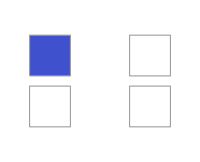
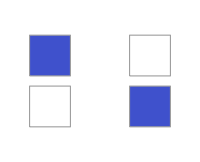
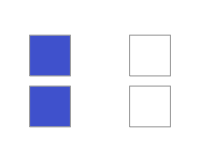
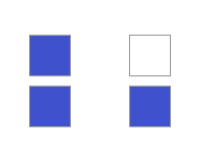
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

Si evolucionamos todos los sistemas con esas reglas podemos encontrar un comportamiento repetido entre la regla  y . Las cuales convierten todo a 0 y todo a 1 respectivamente, pero si hacemos una permutación en los colores (estados), obsevarvamos que obtenemos la otra regla. Para asociar todas estas reglas, utilizamos la función  InverseRules, que recibe el numero de regla, estados y numero de vecinos y devuelve todas las reglas con el mismo comportamiento. 
Adicionalmente, se puede usar la función getAlluniqueRules que solo recibe el numero de estados y de vecinos y crea todas las asociones de ese espacio de reglas. Por ejemplo, estos son los comportamientos unicos para 2 estados y un vecino:

```mathematica
getAllUniqueRules[2,1]
```

{0→{0,3},1→{1},2→{2}}

Si asumimos que el comportamiento de la regla  es el mismo que el de la regla , entonces reducimos aun mas el numero de comportamientos diferentes, sin embargo, la regla  no es reversible, por lo que no exactamente lo mismo, pero si tiene el mismo tipo de atractor. 
Las reglas  y  por otro lado si son reversibles y son las reglas inversas de si mismas.

Estos son los comportamientos unicos para 3 estados. Nuevamente encontramos el patrón de la regla , pero ademas, tenemos nuevos comportamientos

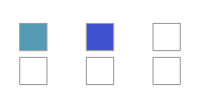
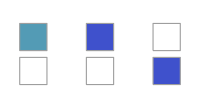
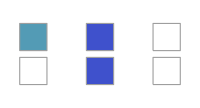
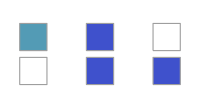
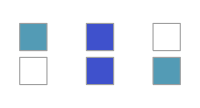
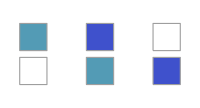
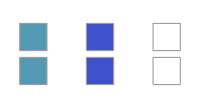
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
urs3=getAllUniqueRules[3,1];
Grid[Partition[RulePlot[CellularAutomaton[{#,3,0}],ColorRules->colorRules,ImageSize->200,PlotLegends->Placed[Subscript[#,3,1], Below]]&/@Keys[urs3],UpTo[4]]]
```

: Sigue el comportamiento de la regla .

: Es una regla con un atractor con periodo 2 pero que no es reversible. Esta regla guarda cierta similitud con  por tener un atractor periodico.

: Esta regla tiene 2 atractores de punto fijo. Esta regla guarda cierta similitud con .

: Esta regla tiene 1 atractor de punto fijo. Esta regla guarda cierta similitud con .

: Esta regla tiene 1 atractor periodico y 1 atractor de punto fijo. Por lo que guarda similitud con las reglas  y .

: La regla  tiene el mismo comportamiento que , pues es un atractor cuyo periodo se define por el numero de estados y el mismo es la regla inversa.

: La regla  tiene  el mismo comportamiento que , pues es un atractor constante con periodo de 1 y es la inversa de si mismo.

Hacer el analisis manual resulta exhaustivo y poco practico porque aunque decimos que “guarda similitud” por la forma en como se comporta su atractor, no tenemos una metrica o una forma consistente de definir dichas relaciones, es por eso, que en lugar de explorar mediante un analisis en individual se busca definir una asociación directa entre ellas.

Para realizar las pruebas se utiliza el siguiente elemento iconizado que almacena todos los comportamientos unicos para los primeros 7 estados. Aunque la vecindad sea 1, aun existen  reglas, por lo que el calculo crece exponencialmente.

```mathematica
urs=;
```

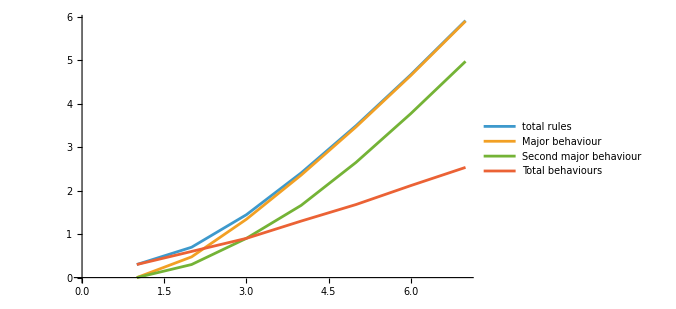

```mathematica
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500
]
```

A continuación, se muestran las reglas agrupadas por numeros de estados. Podemos observar que que todas todas las reglas de  estados son un subconjunto de las reglas con  estados, con la diferencia de que al nuevo estado se le asigna una transición a 0 (el primer estado).

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=50},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules,
Mesh->True,
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

La primer hipotesis es que existia una una forma de generar toda esa secuencia mediante un algoritmo o una formula, y depues existia una función que extraia unicamente las reglas que pertenecian a ese espacio. Esto no se pudo demostrar ya que la secuencia generada es aleatorio o almenos no se pudo encontrar una patrón universal, sino unicamente patrones aislados. Resulta interesante como dentro de la misma definición de los automatas celulares podemos encontrar estas formas complejas.

La siguiente hipotesis era que existe un mapeo entre las reglas que nos permite movernos entre espacios de CAs. Es decir, nosotros podemos movernos de la regla  a la  unicamente añadiendo un nuevo estado que apunte al estado 0. Pero surge la pregunta, ¿Tienen todos el mismo comportamiento? Vamos a mostrar las evoluciones para unos ejemplos.

Reglas {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Reglas {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

Observamos que el comportamiento es practicamente el mismo, pues el ultimo estado unicamente realizando una llamada al primero. Por lo que inferimos 2 cosas de aqui. Si la regla  es reversible, la regla  no lo es, donde x y  tienen el mismo vector de regla. 
Ahora, si nosotros podemos aplicar la función de añadir un nuevo con transición el elemento vacio, tambien debe de ser posible de realizar el proceso inverso, es decir, a una regla cuyo ultimo estado tenga una transición al 0 puede ser eliminida siempre y cuando ningún otro estado tenga una transición al ultimo estado. Esto se cumple para los ejemplos ya mostrados, por lo que estamos haciendo es movernos entre los subconjuntos del espacio de reglas. Pero existen casos excepcionales que no parecen cumplir con esto, por ejemplo, la regla , que si le quitamos las ultimas transiciones obtenemos las siguientes reglas:

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules,Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

Pero las reglas  ni  no pertenencen a la lista de comportamientos unicos, sin embargo, podemos aplicar la función InverseRules para encontrar el representante de ese ese comportamiento y descubirir de donde viene here dado ese patrón. Haciendo esto, Descubrimos que la regla  tiene el siguiente patrón aplicando las dos posibles funciones. Este proceso finaliza hasta que no es posible realizar ninguna de las 2 operaciones.

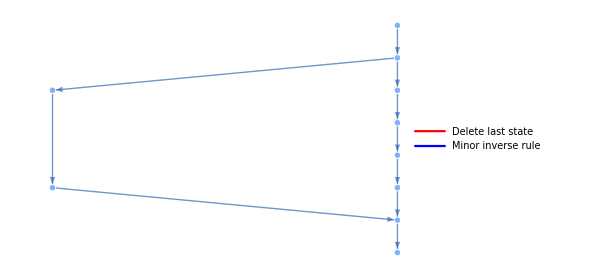

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules,
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

Podemos replicar este proceso para cualquier regla, sin importar el numero de estados, a continuación se muestran algunos ejemplos para diferentes numeros de estados.

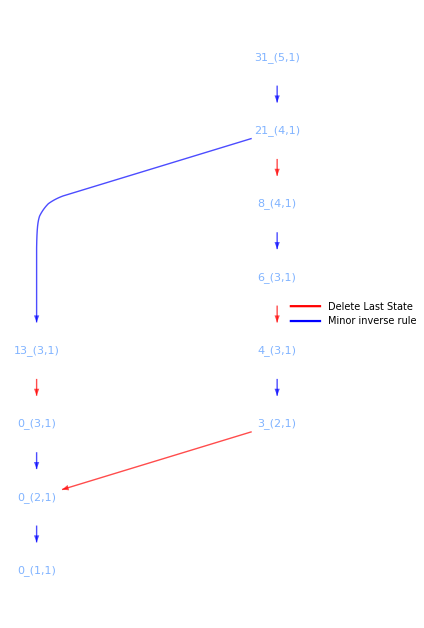
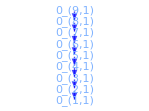
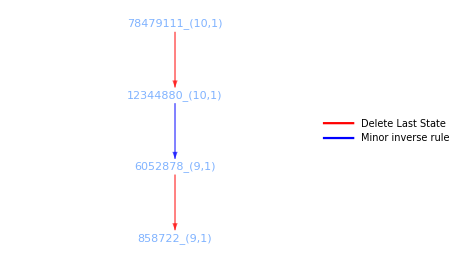
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{rulialGraph[getTransitions[{31,5,0}]],
rulialGraph[getTransitions[{0,9,0}]],
rulialGraph[getTransitions[{78479111,10,0}]]
}}]
```

A continuación se muestra el hipergrafo de todas las relaciones existentes. Cada nota contiene a toras las reglas con el mismo comportamiento, son los elementos que comparten la malla. La altura representa el numero de estados y las flechas hacia abajo apuntan a la regla de la cual imitan el comportamiento. Como ya se habia demostrado, existen reglas que no heredan de otras, es decir, que su comportamiento es unico. Con esto, ademas de reducir significamente el numero de comportamientos al añadir mas estados, tambien se muestran las relaciones de comportamiento.

```mathematica
Import["./trans_0d.pdf"][[1]]
```

-Graphics-

Vamos a generar el grafo que contenga todas estas conexiones. Aunque tecnicamente la mejor definición es un hypergrafo es una función que no se encuentra bien optimizada en Mathematica. Este grafo va a acontener todas las relaciones de 5 estados. Y va a atener la nomenclatura propuesta. Si en algun punto es necesario actualizar la nomenclatura a la dimensión unicamente sera necesario añadir otro subindice a todos estos elementos, nada complicado. 
Ahora bien, este grafo tiene que tener todas las relaciones: inversas, espejo y reducción de estados:

```mathematica
edge={};
edgeStyle={};
```

```mathematica
s=3;
n=1;
rules=Subscript[#,s,n]&/@Range[0,s^(s^n)-1];
{edge,edgeStyle}=addData[rules,edge,edgeStyle];
```

```mathematica
g=Graph[edge,EdgeStyle->edgeStyle];
```

```mathematica
WeaklyConnectedGraphComponents[reduce[g]][[1]]
```

$Aborted

## One Dimensional CA

Hasta el momento solo hemos visto autoamtas celulares adfimensionales. Tecnicamente, no solo autoamtas celulares sino simples maquinas de estados. Ahora, vamos a iniciar aumentando la dimensionalidad. Para esto, podemos iniciar con la configuración mas simple de un automata celular de una dimensión. Imaginemos una linea infinita de celulas, pero cuya vecindad esta definida por un unico elemento.  Este no necesariamente tiene que ser el mismo, pero todas estas configuraciones tienen las propiedades heredadas de un CA adimensional. La información solo considera un estado. Esta propiedad de tener un solo vecino vemos que se hereda en combinaciones futuras, pero eso ser vera continuación.
Otra cosa, si utilizamos un unico estado, no importa el numero de vecinos que tengamos, porque todos tendran la misma regla: , por lo que nuevamente, es la regla absoulta. Por el momento, podemos seguir utilizando la misma nomenclatura .

```mathematica
CaRulePlot[{0,1,1/2}]
```

-Graphics-

Podemos iniciar con las asociaciones aunque sean triviales. En esta regla, podemos ignorar el estado de la izuiqerda o el de la derecha y tenemos el mismo comportamiento. Por lo que la transición no depende de ninguno de los estados. ¿Podemos decir que la regla  proviene de ?

Ahora si, vamos a ver el comportamiento con 2 estados y dos vecinos, la primer configuracion en una dimension con comportmaiento no trivial:

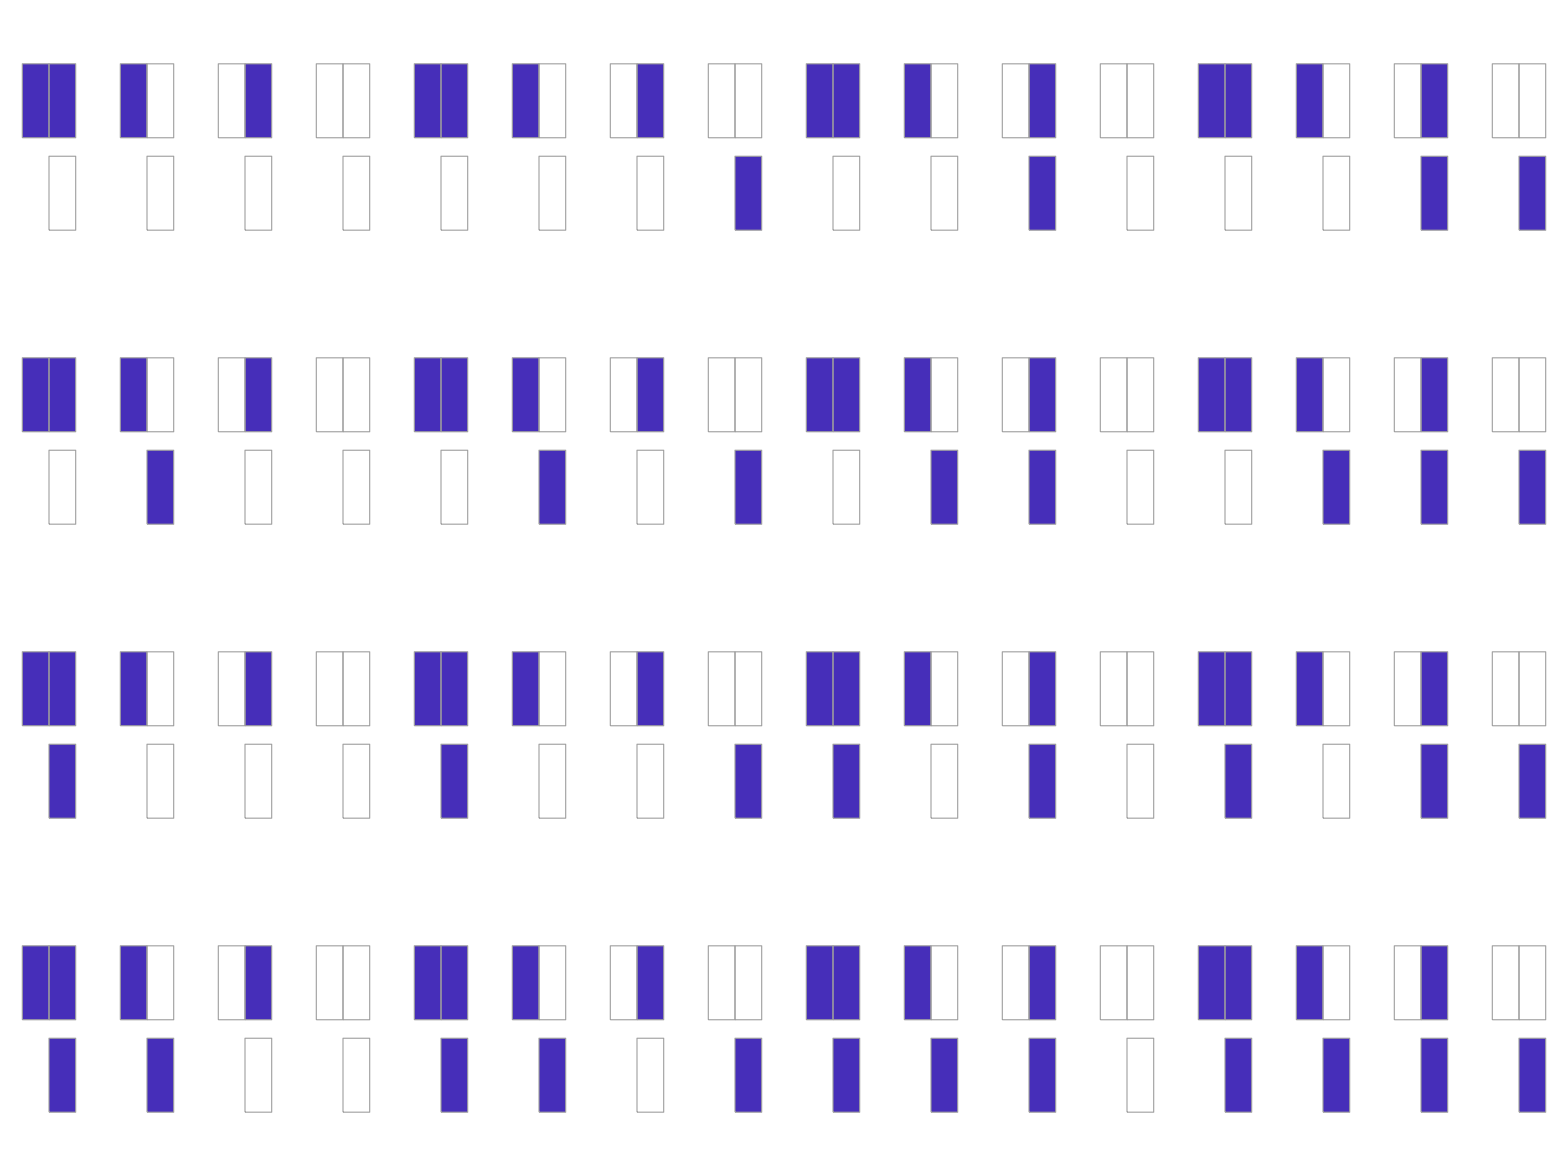

```mathematica
Grid[Partition[CaRulePlot[{#,2,1/2}]&/@Range[0,2^2^2-1],4]]
```

Al igual que antes, podemos encontrar ciertas relaciones que iremos descartando de manera manual y despues de forma algoritmica. A diferencia de antes que no teniamos una base, ahora podemos aplicar ciertos filtros, el primer es encontrar las reglas que pertenecen a CA adimensionales. Primero restringimos el numero de ellos buscando las permutaciones de estados:

{0→{0,15},1→{1,7},2→{2,11},3→{3},4→{4,13},5→{5},6→{6,9},8→{8,14},10→{10},12→{12}}

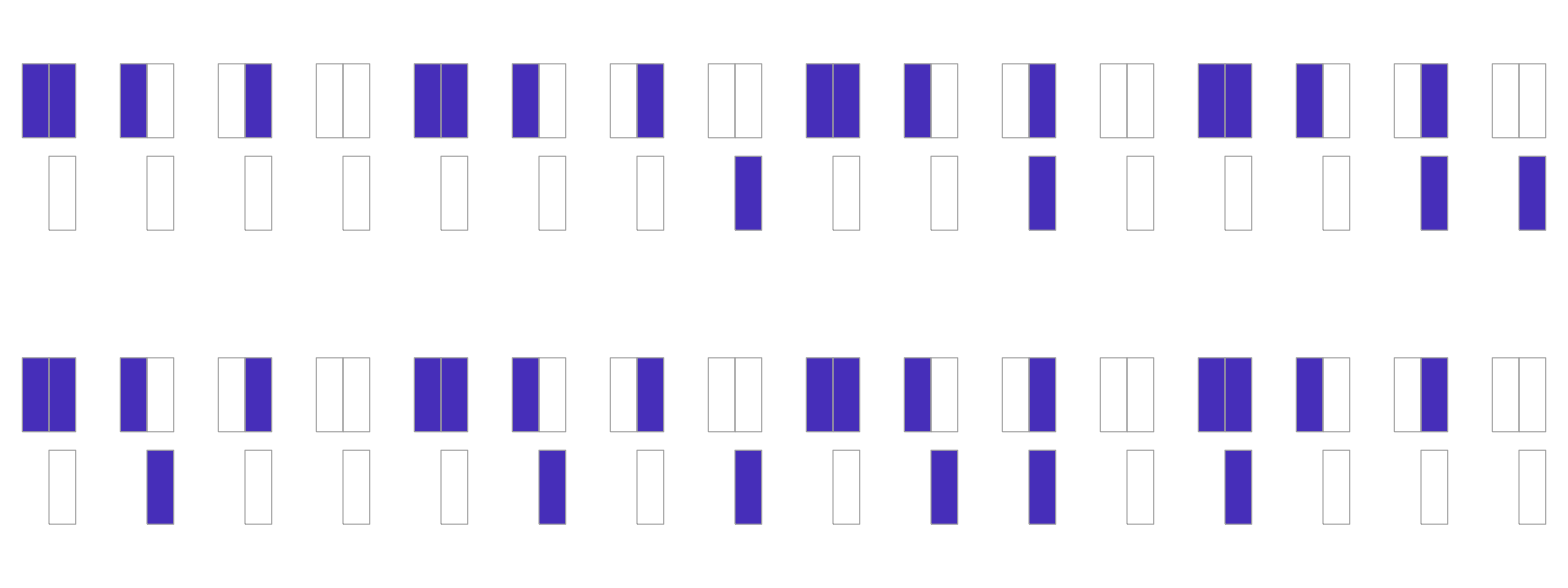

```mathematica
assoc=#[[1]]->#&/@DeleteDuplicates[InverseRules[{#,2,1/2}]&/@Range[0,15]]
Grid[Partition[CaRulePlot[{#[[1]],2,1/2}]&/@assoc,4]]
```

Ahora, necesitamos una función additional, porque los CA adimensionales son simetricos, pero aqui tenemos reglas como las siguientes, cuyo comportamiento se encuentra invertido:

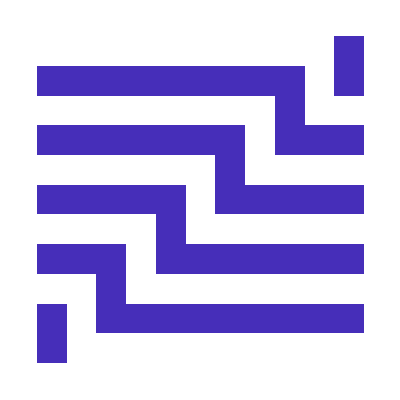
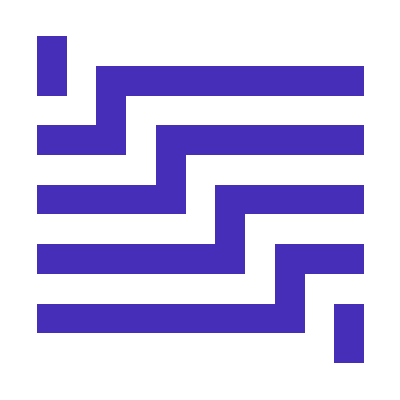
-Graphics- | -Graphics-

```mathematica
init={{1},0};
Grid[{{
RulePlot[CellularAutomaton[{3,2,ReverseSort[{{0},{1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules],
RulePlot[CellularAutomaton[{5,2,ReverseSort[{{0},{-1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules]}
}]
```

Sin embargo, para el notebook de Mathematica es necesario tambien hacer un cambio, y es definir la vecindad manualmente, porque tradicionalemnte se escribe como CellularAutomaton[{3,2,1/2}] pero la vecindad tambien tiene que ser invertida, es decir, ya no se toma el lado izquierdo, se toma el lado derecho, osea que los vectores de desplazamiento se invierten y se reorden. Lo que antes era una vecindad definida por {{1},{0}}, en el espejo se cambia por {{0},{-1}}. Sin embargo, al filtrar los espejos podemos seguir utilizando la definición tradicional, pues esos elementos no forman parte de eso. Ademas de las permutaciones de colores de estados, ahora tambien nos interesa agrupar todas aquellas reglas que son sus equivalentes en espejos. A lo mucho, solo puede tener un espejo, porque hay comportamientos que ya son simetricos. Por lo que de 16 reglas, reducimos a tan solo 7 comportamientos unicos:

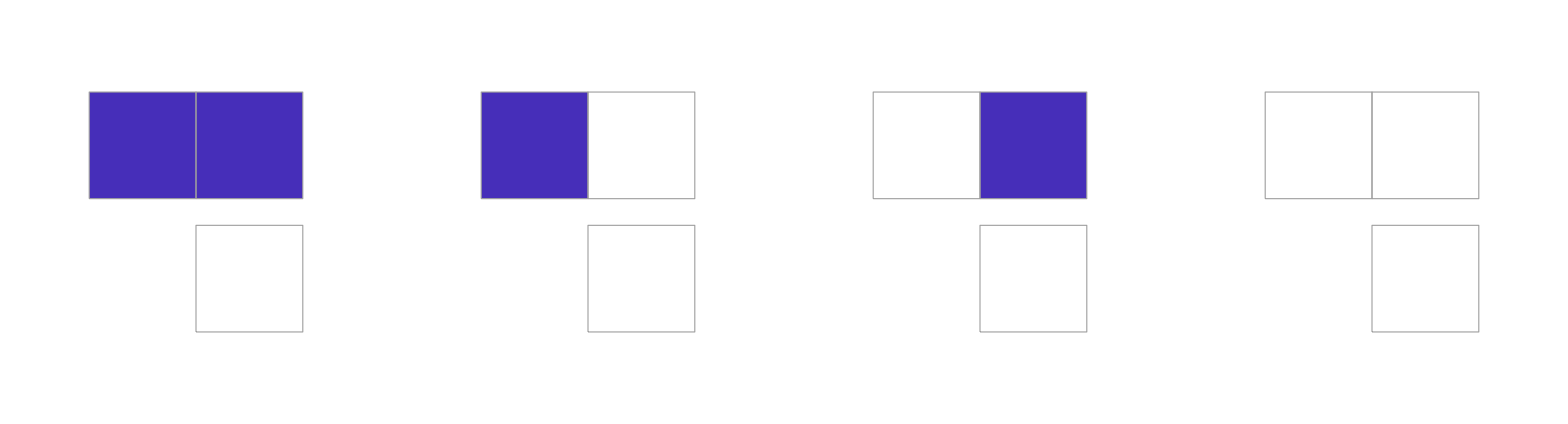
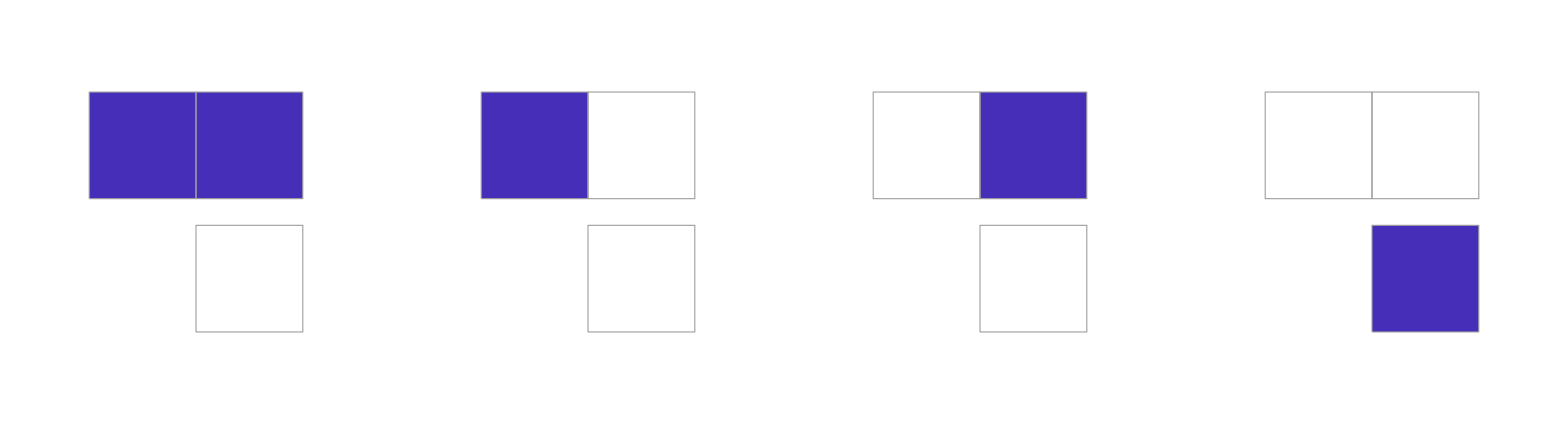
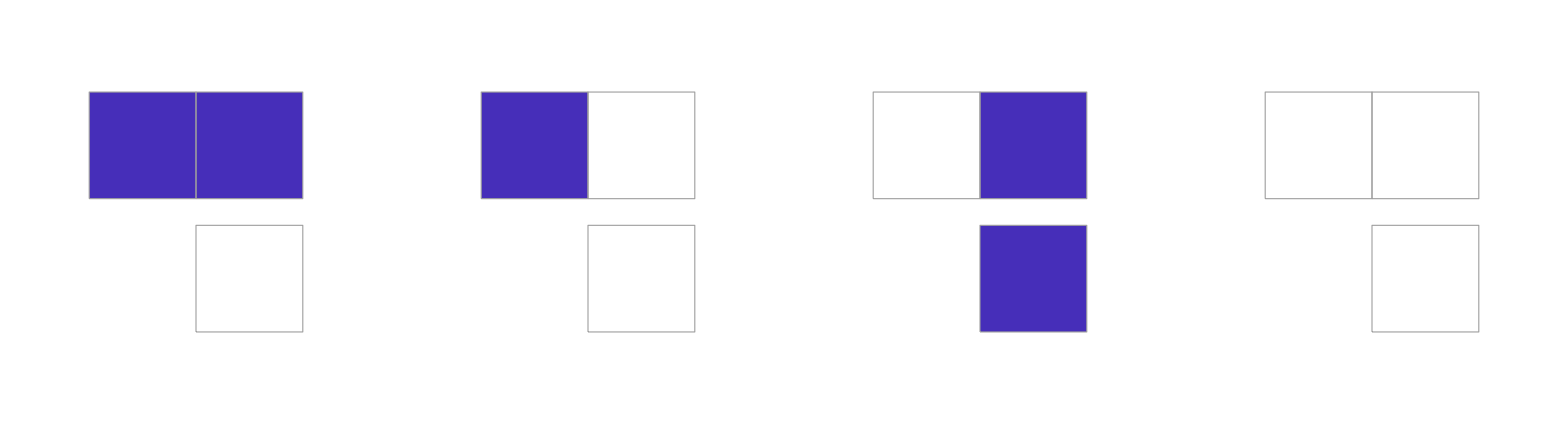
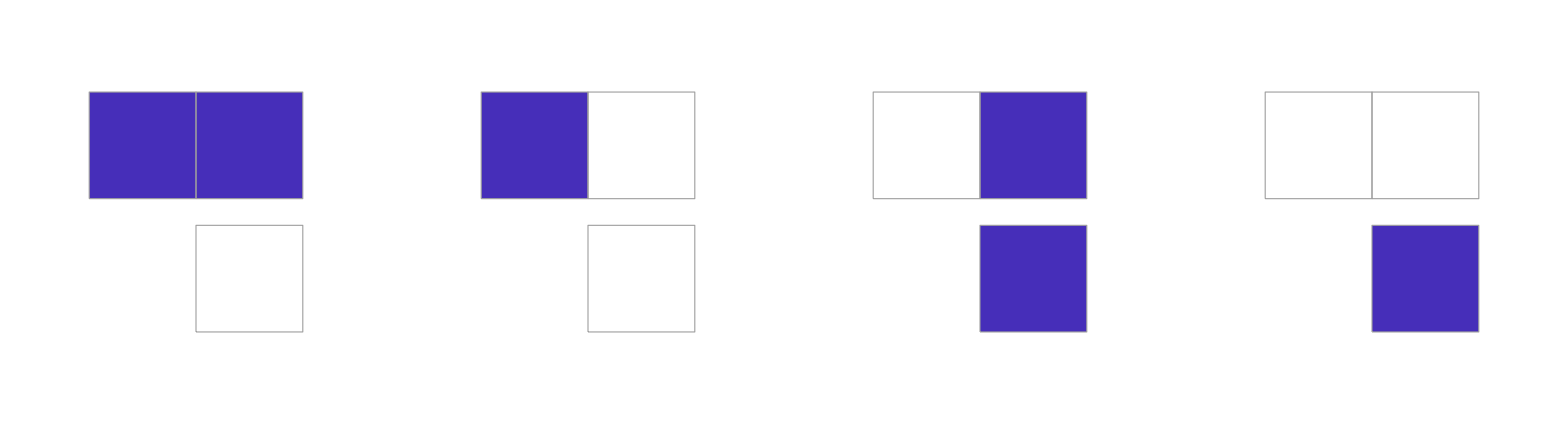
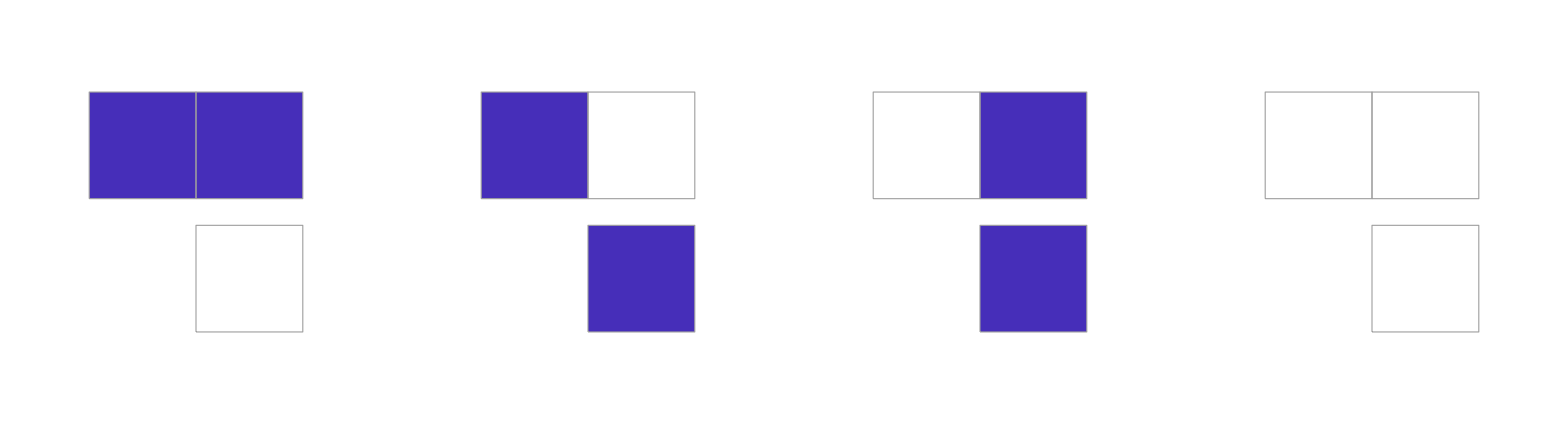
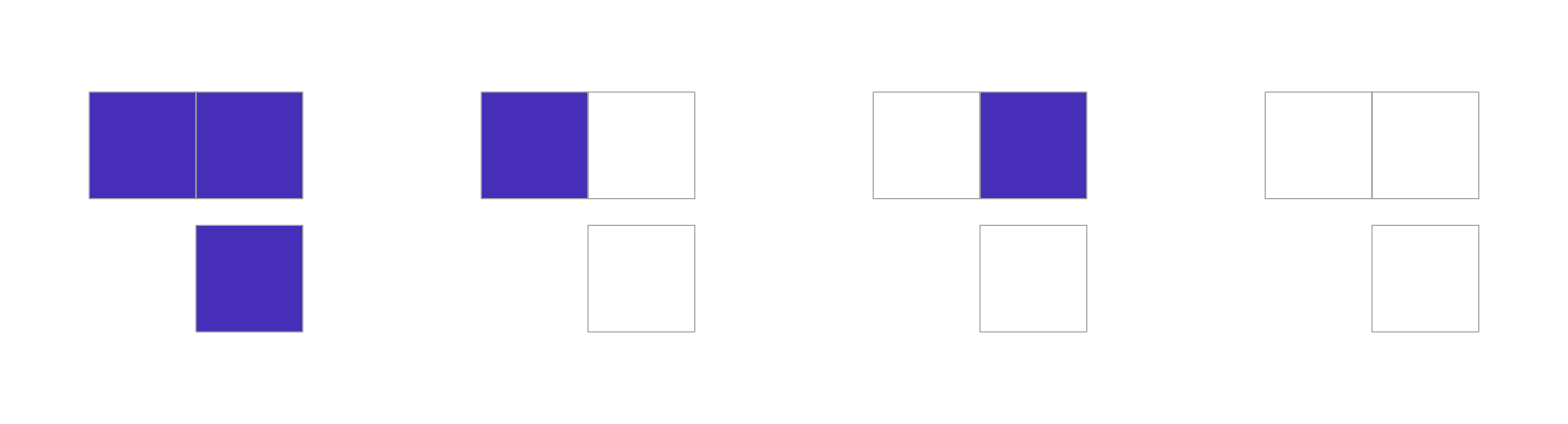
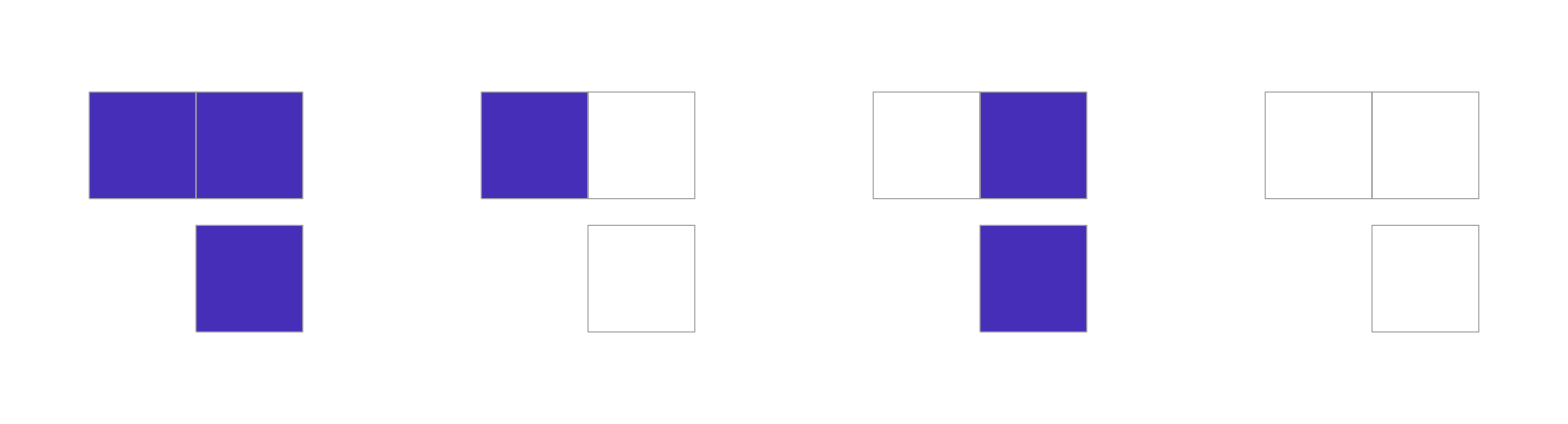
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
#[[1]]->MirrorRules[{#[[1]],2,1/2}]&/@assoc;
Grid[Partition[CaRulePlot[{#,2,1/2}]&/@{0,1,2,3,6,8,10},UpTo[4]]]
```

De estos comportamientos, encontramos 3 relaciones con configuraciones previas.

La regla  no depende de ninguno, al igual que  y

La regla  unicamente depende del vecino de la izquierda, por lo que imita a la regla

La regla  unicamente depende del vecino de la derechoa, por l oque imita a la regla

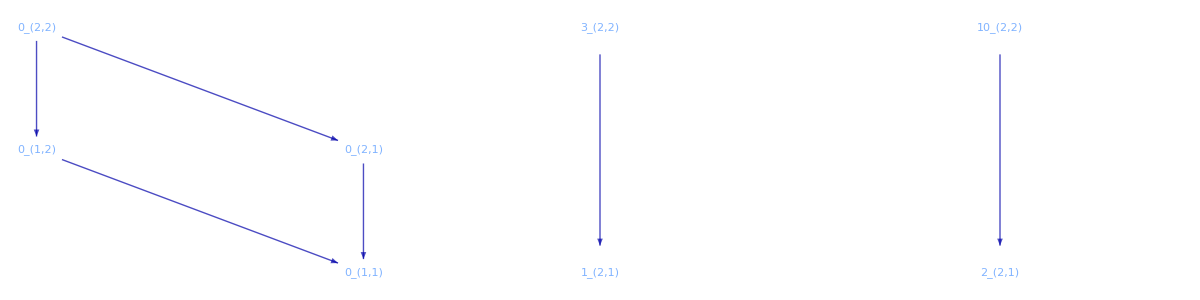

```mathematica
Grid[{{rulialGraph[{{0,2,1/2}->{0,1,1/2},{0,1,1/2}->{0,1,0},{0,2,1/2}->{0,2,0},{0,2,0}->{0,1,0}}],
rulialGraph[{{3,2,1/2}->{1,2,0}}],
rulialGraph[{{10,2,1/2}->{2,2,0}}]}}]
```

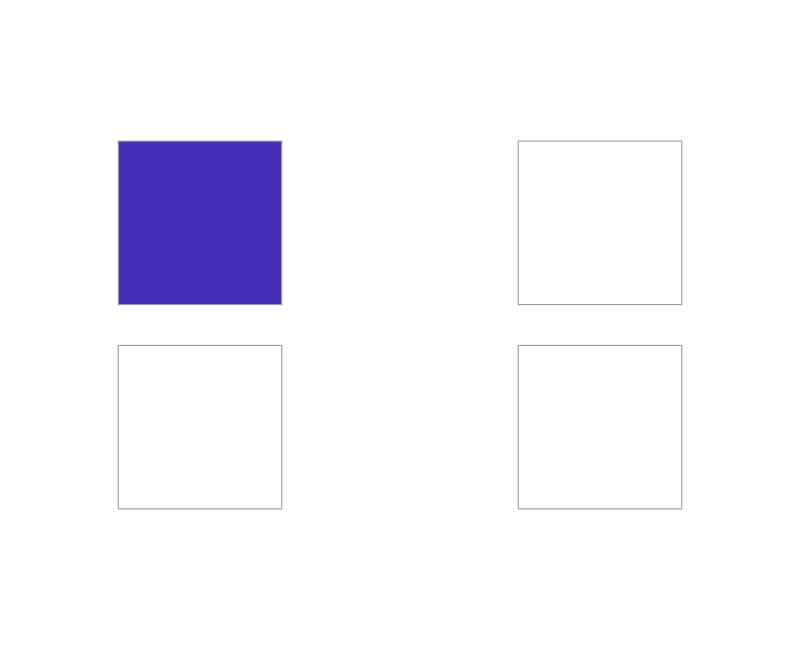

```mathematica
CaRulePlot[{0,2,0}]
```

Las evoluciones de las reglas  y  son exactamente iguales. Para la regla  y  hay que considerar que es el inverso de la celula a la izquierda, por lo que si trasladamos los bloques, a la izquierda, encontramos el mismo comportamiento.

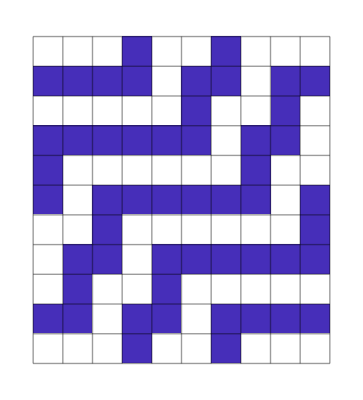
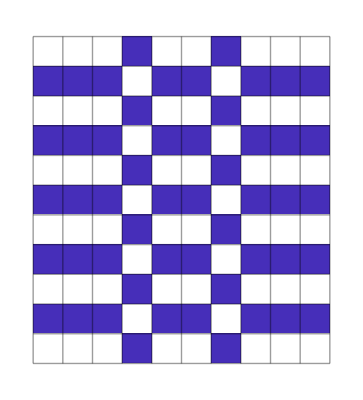
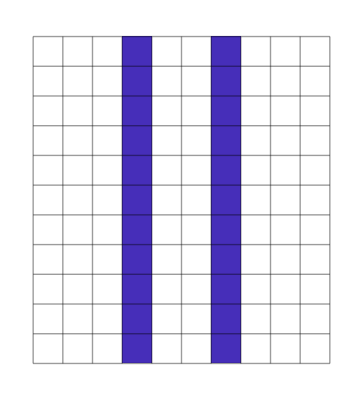
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init={0,0,0,1,0,0,1,0,0,0};
Grid[{RulePlot[CellularAutomaton[#],init,10,PlotLegends->"Icon",ColorRules->colorRules,Mesh->True]&/@{{3,2,1/2},{1,2,0},{10,2,1/2},{2,2,0}}
}]
```

Al final, tenemos solo 4 comportamientos unicos:

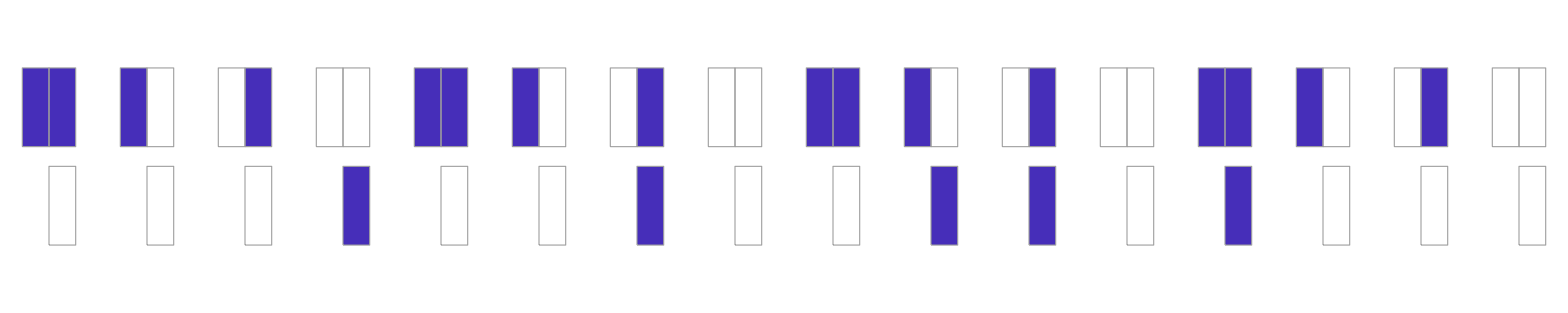

```mathematica
Grid[{CaRulePlot[{#,2,1/2}]&/@{1,2,6,8}}]
```

Con semillas aleatorias, encontramos los siguientes comportamientos, ninguna de ellas es reversible.

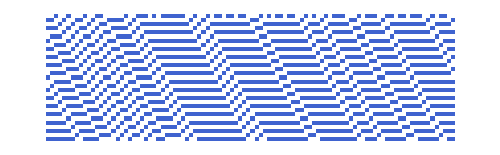
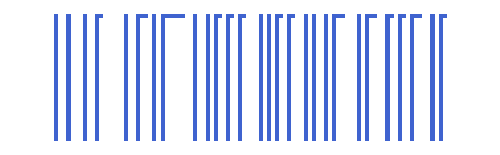
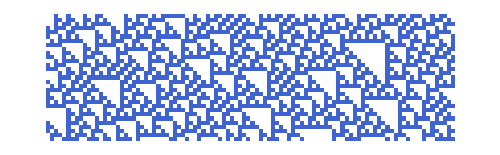
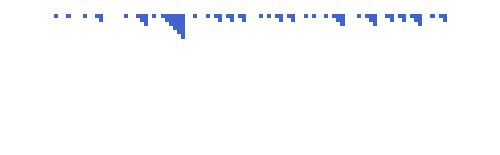
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
Grid[Partition[RulePlot[CellularAutomaton[{#,2,1/2}],init,30,ColorRules->colorRules,ImageSize->500,PlotLegends->"Icon"]&/@{1,2,6,8},2]]
```

Podemos aumentar el numero de estados y la vecindad, si aumentamos la vecindad finalmente llegariamos a los ECA. Si aumentamos el numero de estados, tendremos que encontrar la relación de las nuevas reglas y buscar si existe algun comportamiento similar al que ocurre cuando aplicamos la reducción de estudios.
Este analizamos podemos extenderlo para 3 vecinos con 3 estados. Y tenemos ya 4 funciones, 2 de similitud y 2 de herencia.

Las funciones de similitud nos dicen que 2 reglas tienen el el mismo comportamiento dentro del mismo espacio. Las reglas de herencia significan que son reglas cuyo comportmaiento puede ser obtenido mediante una regla ya sea con menos estados o con menos vecinos. El ultimo paso de esta investigación es la reducción de dimensionalidad. Es el paso mas complejo porque hasta ahora los vecinos siempre estan agrupados. Si decimos que tenemos 2 vecinos suponemos que esos 2 vecinos son los 2 vecinos mas cercanos, porque verlo en una linea es bastante sencillo, el problema es intentar verlo ahora en 2 dimensiones. Por proximidad, yo puedo decir que los 2 vecinos mas cercanos tienen 2 posibilidades:

```mathematica
Grid[{{ArrayPlot[{{0,0,0},{1,2,1},{0,0,0}},ColorRules->colorRules[3],Mesh->True],ArrayPlot[{{0,1,0},{1,2,0},{0,0,0}},ColorRules->colorRules[3],Mesh->True]}}]
```

-Graphics-

Y ambos tienen comportamientos totalmente diferentes, porque aunque el numero de reglas y del vector de regla son equivalentes: , uno de ellos tiene una reducción de dimensionalidad porque solo considera los elementos en un eje, en este caso, el primero solo considera la izquierda y la derecha, es indiferente del resto de dimensiones. 
Otro evento que puede pasar, es que ocurra una reducción de vecindad que despues de paso a una reducción de dimensión. 
Adicionalmente, sera necesario empezar a especificar cuuales son las posición de los elementos, porque por ejemplo, hasta el momento, hemos considerado que los vecinos siempre son los mas cercanos al centro, incluso si solo son 2, pero no hemos verificado si esto se cumple para cualquiera 2 vecinos que tomemos. Porque existen algunas configuraciones en donde si es verdad pero otras en donde es necesario indagar a profundidad.

Por ejemplo, ¿las siguientes 5 reglas son las mismas? Nosotros estamos asumiendo que si, pero la unica diferencia es que vecinos estamos tomando. Entonces bajo la definición que estuvimos manejando, todas son la regla , pero sus vecinos estan en diferentes posiciones, que si miramos vbien parecen que tienen el mismo comportamiento pero que unicamente tienen un desplazamiento o un remapeo, pero el comportamiento parece ser el mismo para todos. El triangulo de Sierpinsky pertenece a otro espacio de regla.

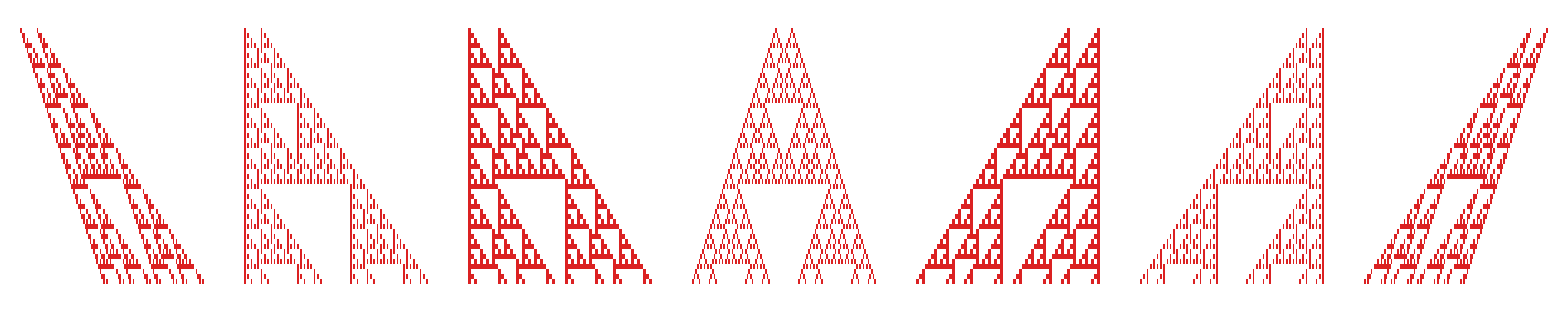

```mathematica
init={{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},0};
Grid[{{
ArrayPlot[CellularAutomaton[{6,2,{{-2},{-1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{0},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{1}}},init,50],ColorRules->colorRules[1]]
}}]
```

A esto hay que sumarle que Mathematica no ofrece una función para mostrar la regla de un CA con una vecindad descentrada, por l oque para analizar todas estas funciones, entonces realmente existen 2 restricciones muy grandes, las cuales son en donde estamos posicionando el vecino.

Parte de esto es que estamos asumiendo que todas estas reglas son iguales, porque cuando hse hace la eliminación de vecinos, no se hace un reacomodo, pero por el momento asumimos que son las mismas.

Finalmente, a conitnuación vamos a explorar la relación de cuantas reglas es posible reducir utilizando estas funciones:

```mathematica
data=<||>;
s=2;
n=1;
rules=Subscript[#,s,n]&/@Range[0,s^s^n-1];
data=addData[rules,data];
g=Graph[DeleteDuplicates@Flatten@Values[data]];
```

```mathematica
data=;
g=;
Length[#]&/@data
```

<|inverse→122572,mirror→39396,state→20242,join→1467,neighbor→95|>

```mathematica
reduce[data]
```

$Aborted

```mathematica
configs={{2,1},{3,1},{4,1},{2,2},{3,2},{2,3}};
unq=Table[
{s,n}=config;
rules=Subscript[#,s,n]&/@Range[0,s^s^n-1];
data=addData[rules];
config->reduce[data]
,{config,configs}];
```

$Aborted

## Otra parte

Ya vimos que existen aun asi muchas reglas que hace falta analizar su comportmaiento, y eso es un poco parte de la clasificación. El problema es que las clasificaciones de las reglas no son funciones, no es que yo pueda definir una función que me determinr a que clase pertenece porque existn muchas formas de intentar hacer esta claificación. 

Bien, tenemos muchas reglas que podemos estudiar, pero dado que con 1 vecino son insignificantes, entonces tenemos 2 opciones, analziar las de 2 vecinos y tres estados o las de 2 estados y 3 vecinos, porque con 2 estados y 2 vecinos solo tenemos 4 comportamientos que son necesarios ser clasificados. Vamos a inicar con als 256 reglas de ECA. Pero solo nos interesan las

```mathematica
rules=Subscript[#,2,3]&/@Range[0,2^2^3-1];
data=reduce[addData[rules]];
rules=Complement[VertexList@data["inverse"],VertexList@data["state"],VertexList@data["neighbor"]]
Length[rules]
g=Graph[Flatten[Values[data]],VertexLabels->"Name"];
Graph[Flatten[EdgeList/@Select[WeaklyConnectedGraphComponents[g],Length[VertexList[#]]>1&]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"];
```

{1_(2,3),2_(2,3),4_(2,3),6_(2,3),7_(2,3),8_(2,3),9_(2,3),11_(2,3),13_(2,3),14_(2,3),18_(2,3),19_(2,3),22_(2,3),23_(2,3),24_(2,3),25_(2,3),26_(2,3),27_(2,3),28_(2,3),29_(2,3),30_(2,3),32_(2,3),33_(2,3),35_(2,3),36_(2,3),37_(2,3),38_(2,3),40_(2,3),41_(2,3),42_(2,3),43_(2,3),44_(2,3),45_(2,3),46_(2,3),50_(2,3),54_(2,3),56_(2,3),57_(2,3),58_(2,3),62_(2,3),72_(2,3),73_(2,3),74_(2,3),76_(2,3),77_(2,3),78_(2,3),94_(2,3),104_(2,3),105_(2,3),106_(2,3),108_(2,3),110_(2,3),122_(2,3),126_(2,3),128_(2,3),130_(2,3),132_(2,3),134_(2,3),138_(2,3),140_(2,3),142_(2,3),146_(2,3),150_(2,3),152_(2,3),154_(2,3),156_(2,3),162_(2,3),164_(2,3),168_(2,3),172_(2,3),178_(2,3),184_(2,3),200_(2,3),232_(2,3)}

74

Todas las reglas 1 siempre estan relacionadas, porque implica una negación de la vecindad cuando todos los elementos son 0. mejor dicho, todas las reglas menores al numero de estados, y el estado define a cual se va a hacer la transicion.

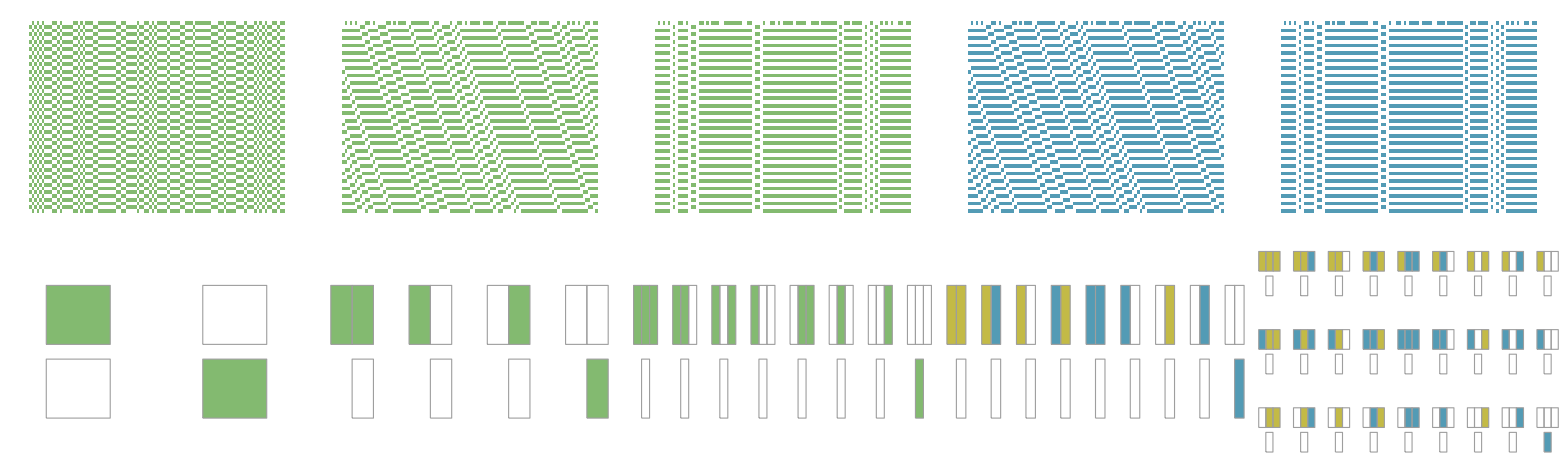

```mathematica
init=RandomInteger[{0,1},100];
rules=Subscript[#1,#2,#3]&@@@{{1,2,1},{1,2,2},{1,2,3},{1,3,2},{1,3,3}};
Grid[Transpose[{CaArrayPlot[#,init,50,ImageSize->250],CaRulePlot[#,ImageSize->Automatic]}&/@rules]]
```

las reglas “s” que equivalen al tamaño de la vecindad tiene el comportamiento de crear un crecimiento en el lado izquierdo, el tamaño de la vecindad define la inclinación. Esto aplica para la regla .

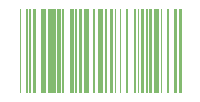
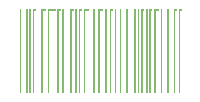
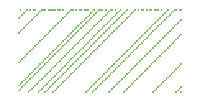
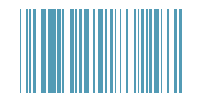
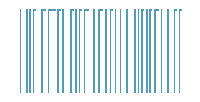
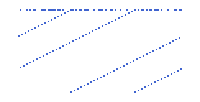
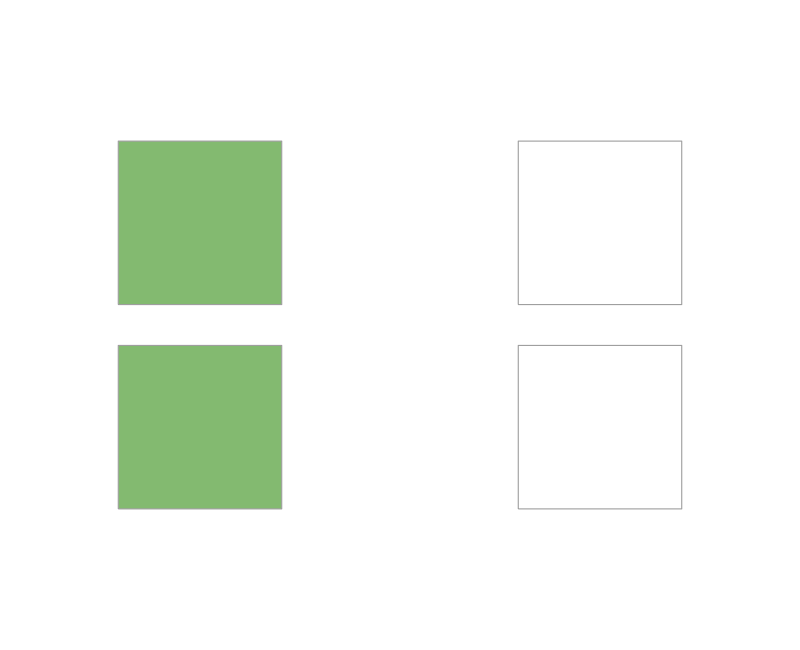
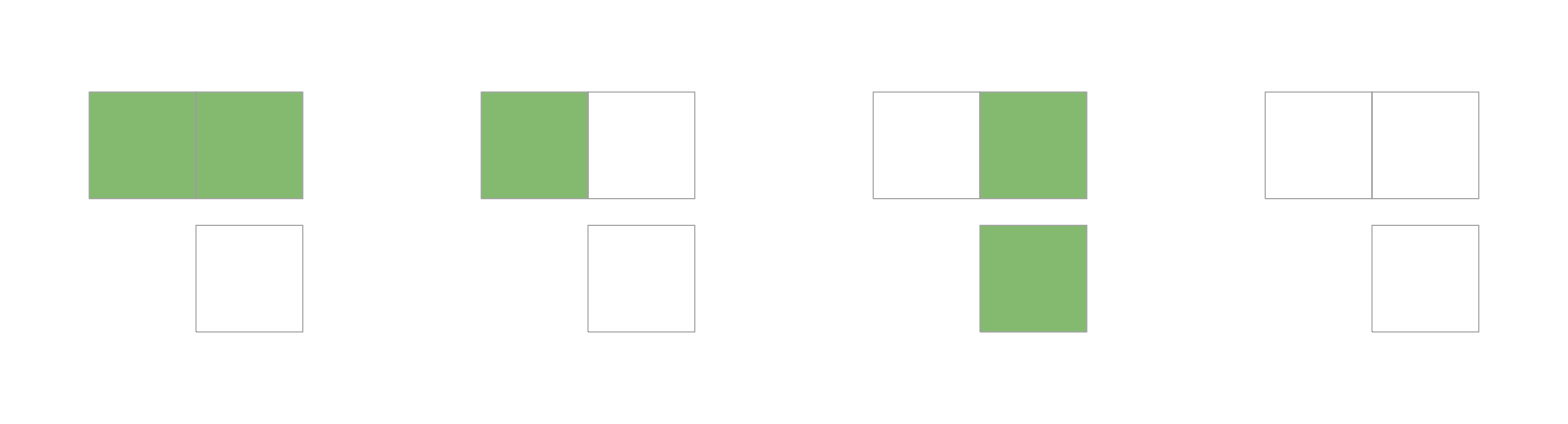
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
rules=Subscript[#1,#2,#3]&@@@{{2,2,1},{2,2,2},{2,2,3},{3,3,1},{3,3,2},{5,5,5}};
Grid[Transpose[{CaArrayPlot[#,init,50,ImageSize->200],CaRulePlot[#]}&/@rules]]
```

```mathematica
r1={Subscript[4, 2,3],Subscript[6, 2,3],Subscript[7, 2,3],Subscript[8, 2,3],Subscript[9, 2,3],Subscript[11, 2,3],Subscript[13, 2,3],Subscript[14, 2,3],Subscript[18, 2,3],Subscript[19, 2,3],Subscript[22, 2,3],Subscript[23, 2,3],Subscript[24, 2,3],Subscript[25, 2,3],Subscript[26, 2,3],Subscript[27, 2,3],Subscript[28, 2,3],Subscript[29, 2,3],Subscript[30, 2,3],Subscript[32, 2,3],Subscript[33, 2,3],Subscript[35, 2,3],Subscript[36, 2,3],Subscript[37, 2,3],Subscript[38, 2,3],Subscript[40, 2,3],Subscript[41, 2,3],Subscript[42, 2,3],Subscript[43, 2,3],Subscript[44, 2,3],Subscript[45, 2,3],Subscript[46, 2,3],Subscript[50, 2,3],Subscript[54, 2,3],Subscript[56, 2,3],Subscript[57, 2,3],Subscript[58, 2,3],Subscript[62, 2,3],Subscript[72, 2,3],Subscript[73, 2,3],Subscript[74, 2,3],Subscript[76, 2,3],Subscript[77, 2,3],Subscript[78, 2,3],Subscript[94, 2,3],Subscript[104, 2,3],Subscript[105, 2,3],Subscript[106, 2,3],Subscript[108, 2,3],Subscript[110, 2,3],Subscript[122, 2,3],Subscript[126, 2,3],Subscript[128, 2,3],Subscript[130, 2,3],Subscript[132, 2,3],Subscript[134, 2,3],Subscript[138, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[146, 2,3],Subscript[150, 2,3],Subscript[152, 2,3],Subscript[154, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[164, 2,3],Subscript[168, 2,3],Subscript[172, 2,3],Subscript[178, 2,3],Subscript[184, 2,3],Subscript[200, 2,3],Subscript[232, 2,3]};
```

Estas son las reglas que tienden a evolucionar en 0, estyo se observa de manera experimental, pero si realizamos un analisis es posible encontrar porque estas reglas? Y si si, estas reglas son hijas de la regla 0?:

```mathematica
init=RandomInteger[{0,1},2000];
rules=Select[r1,CellularAutomaton[{#[[1]],#[[2]],(#[[3]]-1)/2},init,2000][[-10]]===ConstantArray[0,Length[init]]&];
init=RandomInteger[{0,1},50];
Grid[Transpose[{CaArrayPlot[#,init,10,ImageSize->125],CaRulePlot[#,ImageSize->125],#}&/@rules]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8_(2,3) | 32_(2,3) | 40_(2,3) | 128_(2,3) | 168_(2,3)

Siempre tiende a la muerte, no existe una configuración inicial que pueda mantener viva a esta regla.

Tiende a a la muerte en todos los escenarios, a excepción del patrón {...,0,1,0,1,...}

Unicamente sobrevive con el patrón {...,1,1,1,...}

Curiosamente, todas las combinaciones de estas reglas comparten sus propiedes. Aunque aqui no aparecen, todas las combinaciones de es

```mathematica
IntegerDigits[#,2,8]&/@{0,8,32,40,128,136,160,168}
```

```mathematica
ArrayPlot[,ColorRules->colorRules[1],Mesh->True]
```

-Graphics-

```mathematica
SeedRandom[101];
initr=RandomInteger[{0,1},10];
initt=Flatten[ConstantArray[{0,1},5]];
inito=ConstantArray[1,10];
initdo={1,0,1,0,1,1,0,1,0,1};
Grid[Transpose[{
Subscript[#,2,3],
CaArrayPlot[Subscript[#,2,3],initr,7,ImageSize->80],
CaArrayPlot[Subscript[#,2,3],initt,7,ImageSize->80],
CaArrayPlot[Subscript[#,2,3],inito,7,ImageSize->80],
CaArrayPlot[Subscript[#,2,3],initdo,7,ImageSize->80]
}&/@{0,8,32,40,128,136,160,168}]]
```

0_(2,3) | 8_(2,3) | 32_(2,3) | 40_(2,3) | 128_(2,3) | 136_(2,3) | 160_(2,3) | 168_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

La condición que siguen todas estas reglas es todas mueren si tienen 2 ceros seguidos. Podemos seguir la regla de que 1 + 1 = 3 pero si 1 + 2 = 2 entonces existe una relación, porque la adición de dichas reglas solo es la adición de esos comprotamientos. pero no es del todo cierto. Porque la regla 8 y 0 siempre mueren, la 32 solo sobrevive con un patrón, la 40 sobrevive con una condición, la 128 y 126 sobreviven conun patrón, la 160 con 2 patrones y la 168 con 2 patrones y una condición. De estas reglas, solo encontramos previamente 5 porque las otras 3: 0, 136 y 160 son heredadas de otras reglas por reducción de vecinos:

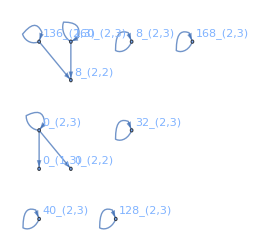

```mathematica
Graph[Flatten[Values[reduce[addData[{Subscript[0, 2,3],Subscript[8, 2,3],Subscript[32, 2,3],Subscript[40, 2,3],Subscript[128, 2,3],Subscript[136, 2,3],Subscript[160, 2,3],Subscript[168, 2,3]}]]]],VertexLabels->"Name"]
```

Nos queda 67 reglas.

```mathematica
r2=Complement[r1,{Subscript[0, 2,3],Subscript[8, 2,3],Subscript[32, 2,3],Subscript[40, 2,3],Subscript[128, 2,3],Subscript[136, 2,3],Subscript[160, 2,3],Subscript[168, 2,3]}]
```

{4_(2,3),6_(2,3),7_(2,3),9_(2,3),11_(2,3),13_(2,3),14_(2,3),18_(2,3),19_(2,3),22_(2,3),23_(2,3),24_(2,3),25_(2,3),26_(2,3),27_(2,3),28_(2,3),29_(2,3),30_(2,3),33_(2,3),35_(2,3),36_(2,3),37_(2,3),38_(2,3),41_(2,3),42_(2,3),43_(2,3),44_(2,3),45_(2,3),46_(2,3),50_(2,3),54_(2,3),56_(2,3),57_(2,3),58_(2,3),62_(2,3),72_(2,3),73_(2,3),74_(2,3),76_(2,3),77_(2,3),78_(2,3),94_(2,3),104_(2,3),105_(2,3),106_(2,3),108_(2,3),110_(2,3),122_(2,3),126_(2,3),130_(2,3),132_(2,3),134_(2,3),138_(2,3),140_(2,3),142_(2,3),146_(2,3),150_(2,3),152_(2,3),154_(2,3),156_(2,3),162_(2,3),164_(2,3),172_(2,3),178_(2,3),184_(2,3),200_(2,3),232_(2,3)}

Podemos intentar encontrar aquellas que tienden a 1, pero deberian de ser las mismas reglas que estas pero en sus versiones inversas, por lo que ya no se encuentran en este conjunto.

Esta es la lista de todas las reglas que tienen una transición a 1 en el ultimo estado, estas se caracterizan porque van a ser oscinaltes entre 2 estados, pero, esta condición es global o puede haber condiciones iniciales que fuercen un unico estado. Curiosamente, tambien tienen la pripeidad de que {0,0,0} -> 1 y {1,1,1} -> 0, por lo que no es imposible que alguna de estas reglas converga a un valor.

```mathematica
Select[r2,IntegerDigits[#[[1]],2,8][[1]]==0&&IntegerDigits[#[[1]],2,8][[-1]]==1&]
```

{7_(2,3),9_(2,3),11_(2,3),13_(2,3),19_(2,3),23_(2,3),25_(2,3),27_(2,3),29_(2,3),33_(2,3),35_(2,3),37_(2,3),41_(2,3),43_(2,3),45_(2,3),57_(2,3),73_(2,3),77_(2,3),105_(2,3)}

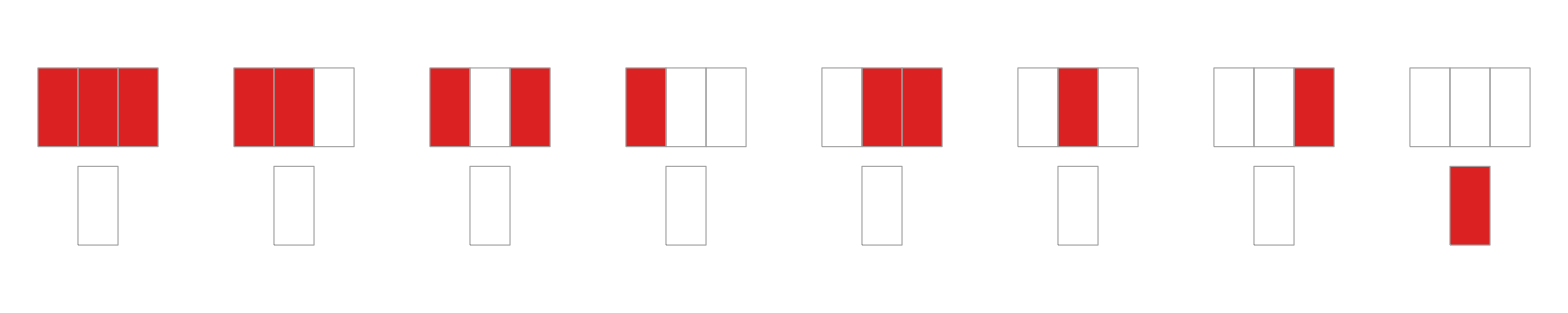
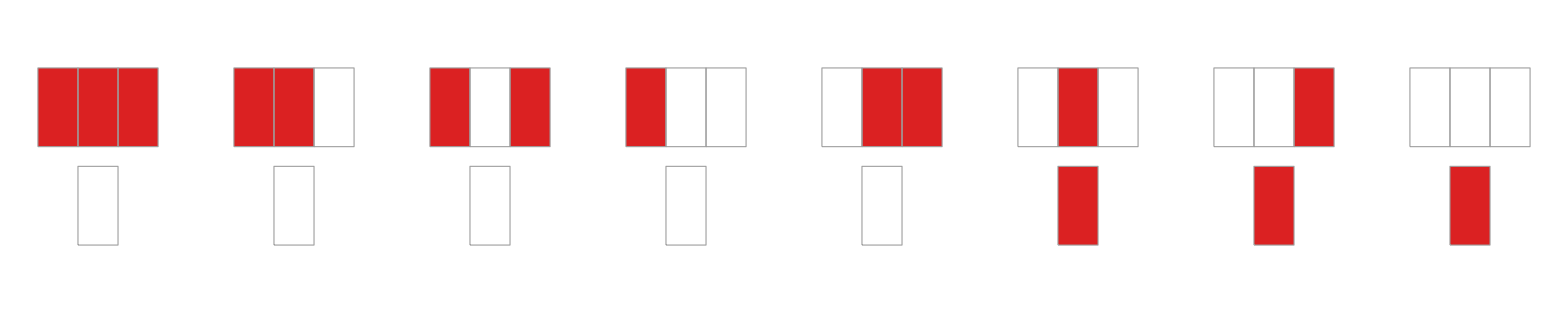
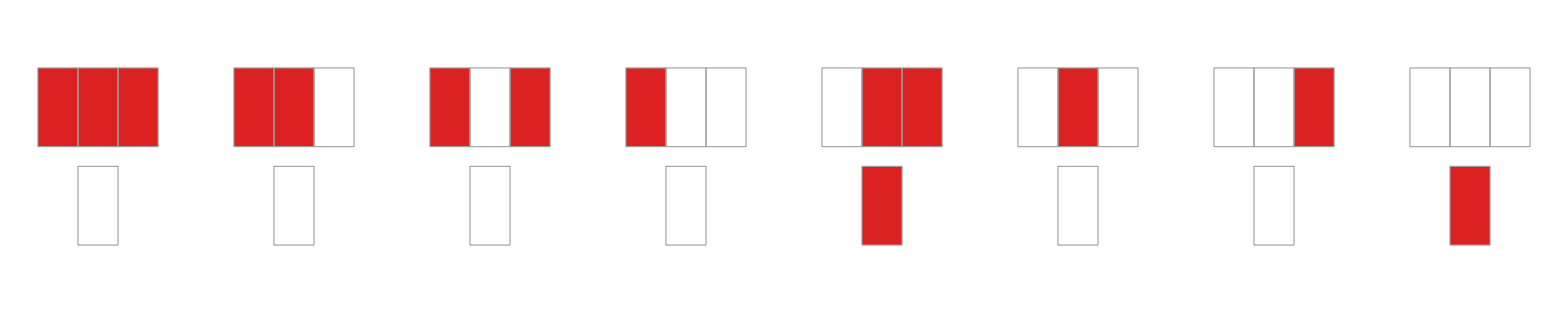
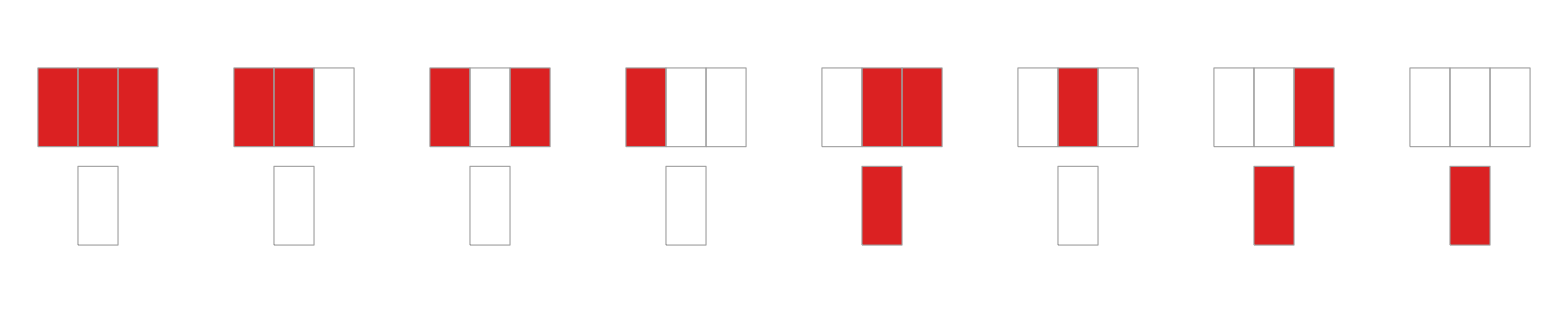
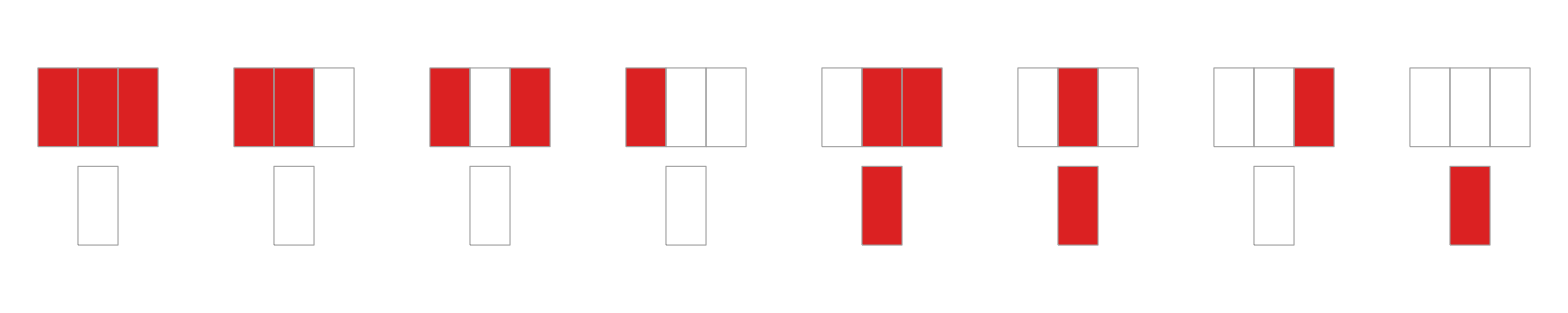
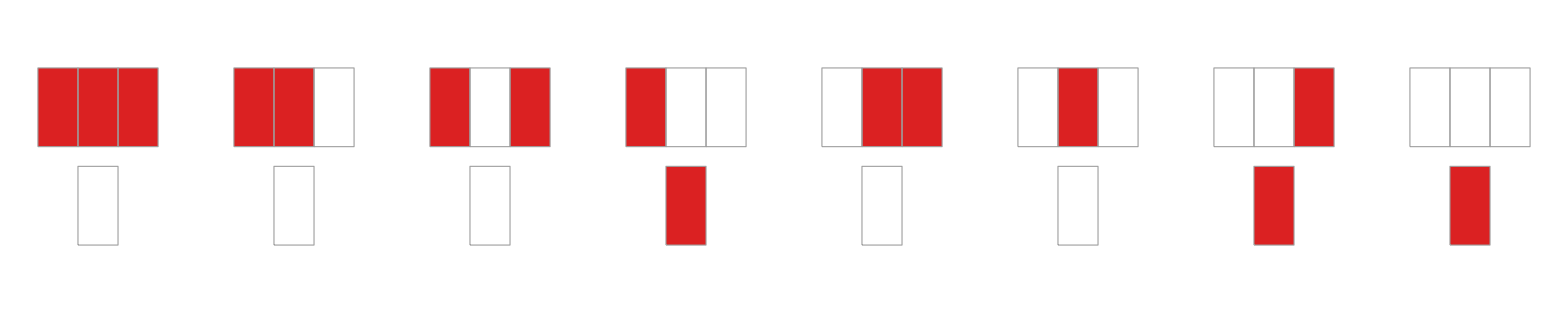
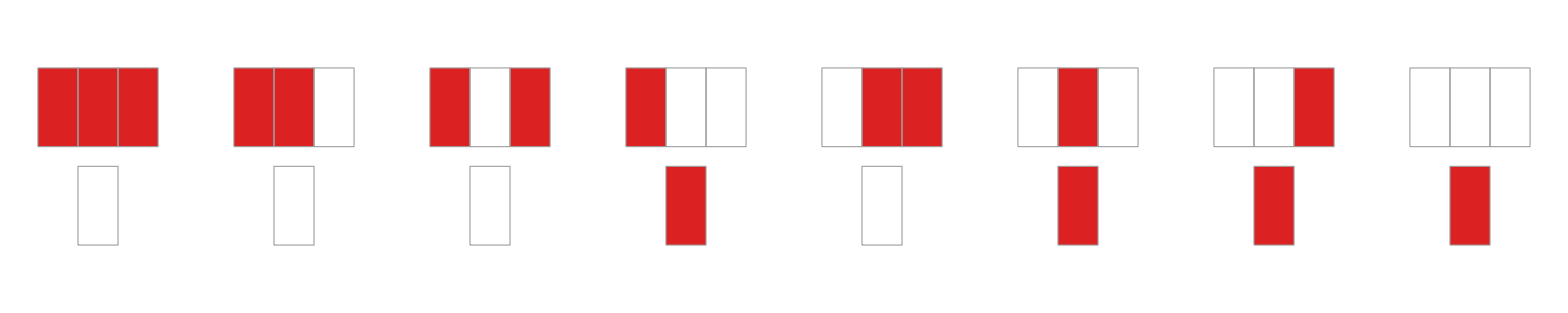
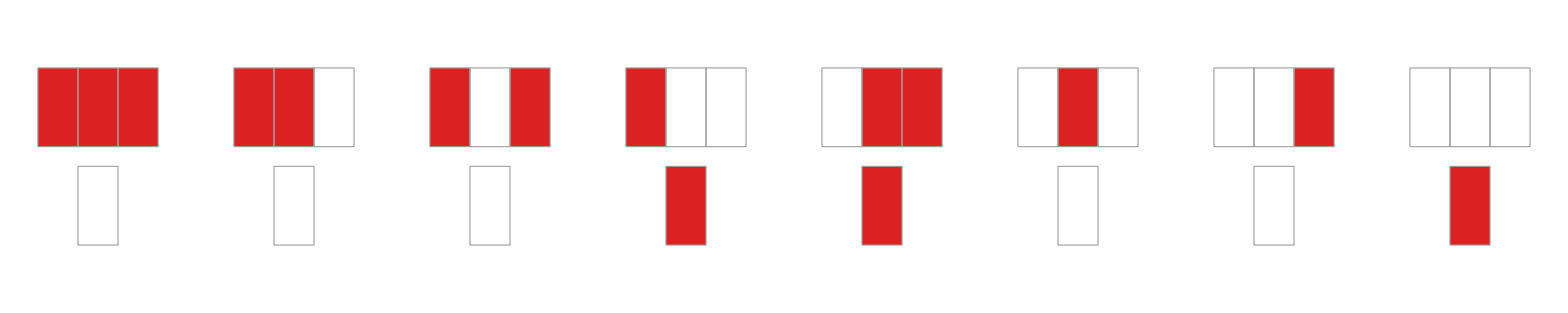
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1_(2,3) | 7_(2,3) | 9_(2,3) | 11_(2,3) | 13_(2,3) | 19_(2,3) | 23_(2,3) | 25_(2,3) | 27_(2,3) | 29_(2,3) | 33_(2,3) | 35_(2,3) | 37_(2,3) | 41_(2,3) | 43_(2,3) | 45_(2,3) | 57_(2,3) | 73_(2,3) | 77_(2,3) | 105_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
r={Subscript[1, 2,3],Subscript[7, 2,3],Subscript[9, 2,3],Subscript[11, 2,3],Subscript[13, 2,3],Subscript[19, 2,3],Subscript[23, 2,3],Subscript[25, 2,3],Subscript[27, 2,3],Subscript[29, 2,3],Subscript[33, 2,3],Subscript[35, 2,3],Subscript[37, 2,3],Subscript[41, 2,3],Subscript[43, 2,3],Subscript[45, 2,3],Subscript[57, 2,3],Subscript[73, 2,3],Subscript[77, 2,3],Subscript[105, 2,3]};
SeedRandom[111];
initr=RandomInteger[{0,1},10];
initt=Flatten[ConstantArray[{0,1},5]];
inito=ConstantArray[1,10];
initdo={1,0,1,0,1,1,0,1,0,1};
Grid[Transpose[{
CaRulePlot[#],
#,
CaArrayPlot[#,initr,7,ImageSize->150],
CaArrayPlot[#,initt,7,ImageSize->150],
CaArrayPlot[#,inito,7,ImageSize->150],
CaArrayPlot[#,initdo,7,ImageSize->150]
}&/@r]]
```

Sin las reglas que terminan y empiezan en inversos inhabilitando la posibilidad de un estado estatico, nos quedan las siguientes reglas:

```mathematica
r3=Complement[r2,{Subscript[7, 2,3],Subscript[9, 2,3],Subscript[11, 2,3],Subscript[13, 2,3],Subscript[19, 2,3],Subscript[23, 2,3],Subscript[25, 2,3],Subscript[27, 2,3],Subscript[29, 2,3],Subscript[33, 2,3],Subscript[35, 2,3],Subscript[37, 2,3],Subscript[41, 2,3],Subscript[43, 2,3],Subscript[45, 2,3],Subscript[57, 2,3],Subscript[73, 2,3],Subscript[77, 2,3],Subscript[105, 2,3]}]
```

{4_(2,3),6_(2,3),14_(2,3),18_(2,3),22_(2,3),24_(2,3),26_(2,3),28_(2,3),30_(2,3),36_(2,3),38_(2,3),42_(2,3),44_(2,3),46_(2,3),50_(2,3),54_(2,3),56_(2,3),58_(2,3),62_(2,3),72_(2,3),74_(2,3),76_(2,3),78_(2,3),94_(2,3),104_(2,3),106_(2,3),108_(2,3),110_(2,3),122_(2,3),126_(2,3),130_(2,3),132_(2,3),134_(2,3),138_(2,3),140_(2,3),142_(2,3),146_(2,3),150_(2,3),152_(2,3),154_(2,3),156_(2,3),162_(2,3),164_(2,3),172_(2,3),178_(2,3),184_(2,3),200_(2,3),232_(2,3)}

Aqui tenemos a las reglas donde los {0,0,0} -> 0 y {1,1,1} -> 1.

```mathematica
Select[r2,IntegerDigits[#[[1]],2,8][[1]]==1&&IntegerDigits[#[[1]],2,8][[-1]]==0&]
```

{130_(2,3),132_(2,3),134_(2,3),138_(2,3),140_(2,3),142_(2,3),146_(2,3),150_(2,3),152_(2,3),154_(2,3),156_(2,3),162_(2,3),164_(2,3),172_(2,3),178_(2,3),184_(2,3),200_(2,3),232_(2,3)}

Estas reglas parecen ser aquellas con mayor numero de atractores, porque no solo pueden convergen hacia ambos puntos, sino que pueden convergen a otras configuraciones. como lineas paralelas, o lineas diagonales. No todas ellas se ven reversibles. Lo que se me ocurre que podemos hacer es evolucionar el sistema en todas las psobiles configuraciones de una condición inicial y analizar como es que se comporta en el tiempo.

```mathematica
r={Subscript[130, 2,3],Subscript[132, 2,3],Subscript[134, 2,3],Subscript[138, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[146, 2,3],Subscript[150, 2,3],Subscript[152, 2,3],Subscript[154, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[164, 2,3],Subscript[172, 2,3],Subscript[178, 2,3],Subscript[184, 2,3],Subscript[200, 2,3],Subscript[232, 2,3]};
SeedRandom[111];
initr=RandomInteger[{0,1},10];
initt=Flatten[ConstantArray[{0,1},5]];
inito=ConstantArray[1,10];
initdo={1,0,1,0,1,1,0,1,0,1};
Grid[Transpose[{
CaRulePlot[#],
#,
CaArrayPlot[#,initr,7,ImageSize->150],
CaArrayPlot[#,initt,7,ImageSize->150],
CaArrayPlot[#,inito,7,ImageSize->150],
CaArrayPlot[#,initdo,7,ImageSize->150]
}&/@r]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
130_(2,3) | 132_(2,3) | 134_(2,3) | 138_(2,3) | 140_(2,3) | 142_(2,3) | 146_(2,3) | 150_(2,3) | 152_(2,3) | 154_(2,3) | 156_(2,3) | 162_(2,3) | 164_(2,3) | 172_(2,3) | 178_(2,3) | 184_(2,3) | 200_(2,3) | 232_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
b=Tuples[{0,1},6];
a={Subscript[130, 2,3],Subscript[132, 2,3],Subscript[134, 2,3],Subscript[138, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[146, 2,3],Subscript[150, 2,3],Subscript[152, 2,3],Subscript[154, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[164, 2,3],Subscript[172, 2,3],Subscript[178, 2,3],Subscript[184, 2,3],Subscript[200, 2,3],Subscript[232, 2,3]};
Manipulate[Grid[{{a[[i]],CaRulePlot[a[[i]]],CaArrayPlot[a[[i]],b[[j]],20]}}],{i,1,Length[a],1},{j,1,Length[b],1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 19 of {2_(2,3),8_(2,3),57_(2,3),138_(2,3),140_(2,3),156_(2,3),162_(2,3),168_(2,3)} does not exist.

CellularAutomaton::initn: The initial condition specification {2_(2,3),8_(2,3),57_(2,3),138_(2,3),140_(2,3),156_(2,3),162_(2,3),168_(2,3)}⟦19⟧ should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

ArrayPlot::mat: Argument CellularAutomaton[{1,2,1},{2_(2,3),8_(2,3),57_(2,3),138_(2,3),140_(2,3),156_(2,3),162_(2,3),168_(2,3)}⟦19⟧,20] at position 1 is not a list of lists.

Part::partd: Part specification a[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 19 of {0_(2,3),3_(2,3),5_(2,3),10_(2,3),12_(2,3),15_(2,3),34_(2,3),51_(2,3),60_(2,3),90_(2,3),136_(2,3),160_(2,3),170_(2,3),204_(2,3)} does not exist.

CellularAutomaton::initn: The initial condition specification {0_(2,3),3_(2,3),5_(2,3),10_(2,3),12_(2,3),15_(2,3),34_(2,3),51_(2,3),60_(2,3),90_(2,3),136_(2,3),160_(2,3),170_(2,3),204_(2,3)}⟦19⟧ should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

ArrayPlot::mat: Argument CellularAutomaton[{0,2,1},{0_(2,3),3_(2,3),5_(2,3),10_(2,3),12_(2,3),15_(2,3),34_(2,3),51_(2,3),60_(2,3),90_(2,3),136_(2,3),160_(2,3),170_(2,3),204_(2,3)}⟦19⟧,20] at position 1 is not a list of lists.

130_(2,3): Solo a 0 con 2 patrones {0,0,...} y si no hay 2 0’s seguidos, crecimiento hacia la izquierda, no reversible.

132_(2,3): Solo con 0s, o si no hay unos solos. Mas bien, La cantidad de unos consecutivos tiene que ser par para que valga 0 Crecimiernto vertical, no reversible. Su atractor a 1 es con todos en 1. esta regla tiene varias funciones, nos permite encontrar el centro de los grupos, o tambien decirnos si es par o impar. Su atractor a 0 es mas constante.

134_(2,3): Parece ser que esta regla siempre esta activa, siempre tiene vida. Porque en todas sus reglas nunca se queda en un solo atractor. Las unicas condiciones excepcionales es todos a 0 o todos a 1, el resto siempre evolucionan. No es como aquellas reglas que nacen y mueren, esta parece ser que si nace nunca muere.

138_(2,3): Igual que la anterior

140_(2,3): Igual que la anterior

142_(2,3): Igual, no es reversible pero la perdida de información es minima, a lo mucho, considero que puede perder un 30% de la información de la condición inicial, pero es suposicion.

146_(2,3) Es la primera regla con comportamiento cruzado de toda la lista, sigfnica que la evolución de la izquierda choca con la de la derecha.  Por lo que da paso a que existan configuraciones iniciales que tiendan a la muerte, pero. Para que tiendan a la vida. Tsambien existen configuraciones que nacen y que mueren dado un numero de pasos, la muerte no es instantanea. Puede que la información perdida en su periodo sea menor que la anterior.

150_(2,3) regresamos con las reglas con solo 1 configuracion por atractor completo.

152_(2,3) igual, sol oqeu ahora crece hacia la derecha.

154_(2,3) lo mismo

156_(2,3) lo mismo

162_(2,3) lo mismo

164_(2,3) tiene crecimiento verticalment unicamente, ai genera el cero pero no el 1-

<|inverse→{130_(2,3)→130_(2,3),130_(2,3)→190_(2,3)},mirror→{130_(2,3)→130_(2,3),130_(2,3)→144_(2,3)},state→{},join→{},neighbor→{}|>

```mathematica
b=Tuples[Range[0,2-1],2^3];
evos=Association[ParallelTable[
ca->(CaArray[ca,#,2^3-1]&/@b)
,{ca,rules[[;;]]}]];
```

```mathematica
{{Subscript[8, 2,3], Subscript[32, 2,3], Subscript[40, 2,3], Subscript[128, 2,3], Subscript[168, 2,3]}}
```

```mathematica
Manipulate[{rules[[ca]],CaRulePlot[rules[[ca]]],ArrayPlot[evos[rules[[ca]]][[i]]]},{ca,1,Length[rules],1},{i,1,Length[b],1}]
```

ArrayPlot::mat: Argument 45_(2,3) at position 1 is not a list of lists.

Part::partd: Part specification rules⟦33⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayPlot::mat: Argument KeyAbsent at position 1 is not a list of lists.

Part::partd: Part specification rules[[33]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

ArrayPlot::mat: Argument rules[[33]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument 45_(2,3) at position 1 is not a list of lists.

Part::partd: Part specification rules⟦33⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayPlot::mat: Argument rules⟦33⟧ at position 1 is not a list of lists.

```mathematica
Keys@Select[evos,Length[DeleteDuplicates[#[[;;,-1]]]]==2&]
```

{128_(2,3)}

```mathematica
{{Subscript[8, 2,3], Subscript[32, 2,3], Subscript[40, 2,3], Subscript[128, 2,3], Subscript[168, 2,3]}}
```

{{8_(2,3),32_(2,3),40_(2,3),128_(2,3),168_(2,3)}}

```mathematica
onePoints=Association@Table[evoCount=Counts[evos[[h]][[;;,-1]]];
points=Sort@Transpose[{FromDigits[#,2]&/@Keys[evoCount],Values[evoCount]}];
points=Sort@Table[
{i[[1,1]],Total[i[[;;,2]]]/(2^2^3)}
,{i,GroupBy[{Count[IntegerDigits[#[[1]],2],1],#[[2]]}&/@points,#[[1]]&]}];
rules[[h]]->points
,{h,1,Length[evos],1}];
```

```mathematica
{{Subscript[8, 2,3], Subscript[32, 2,3], Subscript[40, 2,3], Subscript[128, 2,3], Subscript[168, 2,3]}}
```

```mathematica
Iconize[rules]
Iconize[onePoints]
```

```mathematica
rules=;
```

```mathematica
onePoints=;
```

```mathematica
Manipulate[Grid[{{rules[[h]],ListLinePlot[onePoints[rules[[h]]],PlotRange->All,Mesh->Full,ImageSize->Large,LabelingFunction->Above],CaRulePlot[rules[[h]],ImageSize->Medium]}}],{h,1,Length[evos],1}]
```

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

Callout::copos: {Above} is not a valid position for the placement of callouts.

ListLinePlot::lpn: onePoints[rules⟦22⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rules[[22]] is longer than depth of object.

Callout::copos: {Above} is not a valid position for the placement of callouts.

ListLinePlot::lpn: 
   onePoints[rules[[22]]] is not a list of numbers or pairs of numbers.

Part::partd: Part specification rules[[22]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Callout::copos: {Above} is not a valid position for the placement of callouts.

Callout::copos: {Automatic} is not a valid position for the placement of callouts.

ListLinePlot::lpn: onePoints[32._(2,3)] is not a list of numbers or pairs of numbers.

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

Callout::copos: {Above} is not a valid position for the placement of callouts.

ListLinePlot::lpn: onePoints[rules⟦22⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

Callout::copos: {Above} is not a valid position for the placement of callouts.

ListLinePlot::lpn: onePoints[rules⟦22⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification rules⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
a=onePoints[#]&/@{Subscript[134, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[150, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[178, 2,3],Subscript[184, 2,3]};
ListLinePlot[a,PlotRange->All,Mesh->Full,ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

```mathematica
a=onePoints[#]&/@{Subscript[156, 2,3],Subscript[178, 2,3]};
ListLinePlot[a,PlotRange->All,Mesh->Full,ImageSize->Large,PlotLegends->Automatic,LabelingFunction->Above,PlotRange->All]
```

-Graphics-

Estas son las reglas que tienen una unica transición a 0 y una unica a transición a llenar el espacio, y son las soluciones triviales.

```mathematica
r=Keys[Select[onePoints,MemberQ[#,{0,1/256}]&&MemberQ[#,{8,1/256}]&]]
ArrayPlot[IntegerDigits[#[[1]],2,8]&/@r,Mesh->True,ColorRules->colorRules[1]]
```

{13_(2,3),29_(2,3),35_(2,3),41_(2,3),43_(2,3),57_(2,3),77_(2,3),105_(2,3),134_(2,3),140_(2,3),142_(2,3),150_(2,3),156_(2,3),162_(2,3),178_(2,3),184_(2,3)}

-Graphics-

Estas son las reglas {13_(2,3),29_(2,3),35_(2,3),41_(2,3),43_(2,3),57_(2,3),77_(2,3),105_(2,3)} que tienen transición periodica. 
Estas son las reglas {134_(2,3),140_(2,3),142_(2,3),150_(2,3),156_(2,3),162_(2,3),178_(2,3),184_(2,3)} que tienen los atractores unicos no periodicos.

```mathematica
Grid[Transpose[{#,CaArrayPlot[#,ConstantArray[1,6],2,Mesh->True],CaArrayPlot[#,ConstantArray[0,6],2,Mesh->True]}&/@{Subscript[134, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[150, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[178, 2,3],Subscript[184, 2,3]}]]
```

134_(2,3) | 140_(2,3) | 142_(2,3) | 150_(2,3) | 156_(2,3) | 162_(2,3) | 178_(2,3) | 184_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose@Table[{i,ListLinePlot[DeleteDuplicates[Table[Count[#,1]&/@evo,{evo,evos[i]}]],PlotRange->All,ImageSize->100]},{i,{Subscript[134, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[150, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[178, 2,3],Subscript[184, 2,3]}}]];
```

```mathematica
Grid[Transpose@Table[{i,ListLinePlot[DeleteDuplicates[Table[Count[#,1]&/@evo,{evo,evos[i]}]],PlotRange->All,ImageSize->100]},{i,{Subscript[13, 2,3],Subscript[29, 2,3],Subscript[35, 2,3],Subscript[41, 2,3],Subscript[43, 2,3],Subscript[57, 2,3],Subscript[77, 2,3],Subscript[105, 2,3]}}]];
```

```mathematica
Grid[Transpose@Table[{i,ListLinePlot[DeleteDuplicates[Table[Count[#,1]&/@evo,{evo,evos[i]}]],PlotRange->All,ImageSize->100]},{i,{Subscript[8, 2,3],Subscript[32, 2,3],Subscript[40, 2,3],Subscript[128, 2,3],Subscript[168, 2,3]}}]]
```

8_(2,3) | 32_(2,3) | 40_(2,3) | 128_(2,3) | 168_(2,3)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose@Table[{i,ListLinePlot[DeleteDuplicates[Table[FromDigits[#,2]&/@evo,{evo,evos[i]}]],PlotRange->All,ImageSize->100]},{i,{Subscript[128, 2,3]}}]]
```

128_(2,3)
-Graphics-

La regla  es reversible.

```mathematica
DeleteDuplicates[Sort/@Transpose[Table[FromDigits[#,2]&/@evo,{evo,evos[Subscript[105, 2,3]]}]]]
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}}

```mathematica
a=Keys/@GroupBy[onePoints,Length]
```

<|7→{1_(2,3),11_(2,3),19_(2,3),23_(2,3),33_(2,3),43_(2,3),45_(2,3),142_(2,3),232_(2,3)},3→{2_(2,3),18_(2,3),24_(2,3),36_(2,3),40_(2,3),44_(2,3),46_(2,3),72_(2,3),78_(2,3)},5→{4_(2,3),6_(2,3),9_(2,3),14_(2,3),25_(2,3),26_(2,3),37_(2,3),38_(2,3),54_(2,3),57_(2,3),62_(2,3),77_(2,3),122_(2,3),126_(2,3),156_(2,3),178_(2,3)},6→{7_(2,3),41_(2,3),42_(2,3),56_(2,3),74_(2,3),76_(2,3),108_(2,3),132_(2,3),134_(2,3),140_(2,3),162_(2,3),168_(2,3),172_(2,3)},1→{8_(2,3)},4→{13_(2,3),22_(2,3),28_(2,3),50_(2,3),58_(2,3),94_(2,3),104_(2,3),110_(2,3),130_(2,3),146_(2,3),152_(2,3),164_(2,3)},9→{27_(2,3),29_(2,3),105_(2,3),150_(2,3),184_(2,3)},8→{30_(2,3),35_(2,3),73_(2,3),106_(2,3),138_(2,3),154_(2,3),200_(2,3)},2→{32_(2,3),128_(2,3)}|>

```mathematica
MatrixForm[{#,CaRulePlot[#,ImageSize->Medium]}&/@a[8]]
```

(30_(2,3) | -Graphics-
35_(2,3) | -Graphics-
73_(2,3) | -Graphics-
106_(2,3) | -Graphics-
138_(2,3) | -Graphics-
154_(2,3) | -Graphics-
200_(2,3) | -Graphics-)

```mathematica
onePoints[[1,;;,2]]
Reverse[onePoints[[1,;;,2]]]
```

{131/256,7/32,9/64,1/16,1/32,1/32,1/256}

{1/256,1/32,1/32,1/16,9/64,7/32,131/256}

```mathematica
Select[onePoints,#[[;;,2]]==Reverse[#[[;;,2]]]&];
Keys/@GroupBy[%,Length]
Keys[Select[onePoints,#[[;;,2]]==Reverse[#[[;;,2]]]&]]
```

<|3→{2_(2,3)},1→{8_(2,3)},7→{23_(2,3),43_(2,3),142_(2,3),232_(2,3)},9→{29_(2,3),105_(2,3),150_(2,3),184_(2,3)},5→{57_(2,3),77_(2,3),156_(2,3),178_(2,3)}|>

{2_(2,3),8_(2,3),23_(2,3),29_(2,3),43_(2,3),57_(2,3),77_(2,3),105_(2,3),142_(2,3),150_(2,3),156_(2,3),178_(2,3),184_(2,3),232_(2,3)}

```mathematica
r={Subscript[13, 2,3],Subscript[29, 2,3],Subscript[35, 2,3],Subscript[41, 2,3],Subscript[43, 2,3],Subscript[57, 2,3],Subscript[77, 2,3],Subscript[105, 2,3],Subscript[134, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[150, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[178, 2,3],Subscript[184, 2,3]};
ArrayPlot[IntegerDigits[#[[1]],2,8]&/@r,Mesh->True,ColorRules->colorRules[1]]
```

-Graphics-

```mathematica
simetric=<|3->{Subscript[2, 2,3]},1->{Subscript[8, 2,3]},7->{Subscript[23, 2,3],Subscript[43, 2,3],Subscript[142, 2,3],Subscript[232, 2,3]},9->{Subscript[29, 2,3],Subscript[105, 2,3],Subscript[150, 2,3],Subscript[184, 2,3]},5->{Subscript[57, 2,3],Subscript[77, 2,3],Subscript[156, 2,3],Subscript[178, 2,3]}|>;
```

```mathematica
Grid[Transpose[{CaRulePlot[#],CaArrayPlot[#,Flatten[ConstantArray[{0,0,1},10]],20,ImageSize->250]}&/@simetric[5]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

## Otra

## Otra parte 2

Vamos a intentar explorar si existen algunas reglas con herencia mixta. Hasta el momento solo estuvimos analizando aquellas regla que solo tienen una herencia directa pero que tal si tiene varias?

Medir la longitud no parece tener algun proposito, existe reglas que tienen ciertas relaciones, pero la mayoria de elloas ni siquiera tienen grafos similiares al evolucionar en el tiempo. Vamos a medir la relacion de entradas con salidas, se estan probando todas las entradas pero que hay de las salidas?? Por que ejemplo no es lo mismo tener 5 estructuras que tener 5 atractores.

```mathematica
rules={Subscript[1, 2,3],Subscript[2, 2,3],Subscript[4, 2,3],Subscript[6, 2,3],Subscript[7, 2,3],Subscript[8, 2,3],Subscript[9, 2,3],Subscript[11, 2,3],Subscript[13, 2,3],Subscript[14, 2,3],Subscript[18, 2,3],Subscript[19, 2,3],Subscript[22, 2,3],Subscript[23, 2,3],Subscript[24, 2,3],Subscript[25, 2,3],Subscript[26, 2,3],Subscript[27, 2,3],Subscript[28, 2,3],Subscript[29, 2,3],Subscript[30, 2,3],Subscript[32, 2,3],Subscript[33, 2,3],Subscript[35, 2,3],Subscript[36, 2,3],Subscript[37, 2,3],Subscript[38, 2,3],Subscript[40, 2,3],Subscript[41, 2,3],Subscript[42, 2,3],Subscript[43, 2,3],Subscript[44, 2,3],Subscript[45, 2,3],Subscript[46, 2,3],Subscript[50, 2,3],Subscript[54, 2,3],Subscript[56, 2,3],Subscript[57, 2,3],Subscript[58, 2,3],Subscript[62, 2,3],Subscript[72, 2,3],Subscript[73, 2,3],Subscript[74, 2,3],Subscript[76, 2,3],Subscript[77, 2,3],Subscript[78, 2,3],Subscript[94, 2,3],Subscript[104, 2,3],Subscript[105, 2,3],Subscript[106, 2,3],Subscript[108, 2,3],Subscript[110, 2,3],Subscript[122, 2,3],Subscript[126, 2,3],Subscript[128, 2,3],Subscript[130, 2,3],Subscript[132, 2,3],Subscript[134, 2,3],Subscript[138, 2,3],Subscript[140, 2,3],Subscript[142, 2,3],Subscript[146, 2,3],Subscript[150, 2,3],Subscript[152, 2,3],Subscript[154, 2,3],Subscript[156, 2,3],Subscript[162, 2,3],Subscript[164, 2,3],Subscript[168, 2,3],Subscript[172, 2,3],Subscript[178, 2,3],Subscript[184, 2,3],Subscript[200, 2,3],Subscript[232, 2,3]};
```

```mathematica
space=15;
evos=ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
graphs=Table[
conect=Map[
CaArray[rules[[i]],#,1][[1]]->CaArray[rules[[i]],#,1][[2]]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}];
graphs,
{space,1,10}];
```

```mathematica
evos[[8,;;,2]];
```

```mathematica
DeleteDuplicates[EdgeList[#[[2]]][[;;,2]]]&/@evos[[5,;;1]]
```

{{{1,1,1,1,1},{0,1,1,0,0},{1,1,0,0,0},{0,1,0,0,0},{1,0,0,0,1},{0,0,0,0,0},{1,0,0,0,0},{0,0,0,1,1},{0,0,0,0,1},{0,0,1,1,0},{0,0,1,0,0},{0,0,0,1,0}}}

```mathematica
EdgeList[evos[[5,1,2]]]
```

{{0,0,0,0,0}->{1,1,1,1,1},{0,0,0,0,1}->{0,1,1,0,0},{0,0,0,1,0}->{1,1,0,0,0},{0,0,0,1,1}->{0,1,0,0,0},{0,0,1,0,0}->{1,0,0,0,1},{0,0,1,0,1}->{0,0,0,0,0},{0,0,1,1,0}->{1,0,0,0,0},{0,0,1,1,1}->{0,0,0,0,0},{0,1,0,0,0}->{0,0,0,1,1},{0,1,0,0,1}->{0,0,0,0,0},{0,1,0,1,0}->{0,0,0,0,0},{0,1,0,1,1}->{0,0,0,0,0},{0,1,1,0,0}->{0,0,0,0,1},{0,1,1,0,1}->{0,0,0,0,0},{0,1,1,1,0}->{0,0,0,0,0},{0,1,1,1,1}->{0,0,0,0,0},{1,0,0,0,0}->{0,0,1,1,0},{1,0,0,0,1}->{0,0,1,0,0},{1,0,0,1,0}->{0,0,0,0,0},{1,0,0,1,1}->{0,0,0,0,0},{1,0,1,0,0}->{0,0,0,0,0},{1,0,1,0,1}->{0,0,0,0,0},{1,0,1,1,0}->{0,0,0,0,0},{1,0,1,1,1}->{0,0,0,0,0},{1,1,0,0,0}->{0,0,0,1,0},{1,1,0,0,1}->{0,0,0,0,0},{1,1,0,1,0}->{0,0,0,0,0},{1,1,0,1,1}->{0,0,0,0,0},{1,1,1,0,0}->{0,0,0,0,0},{1,1,1,0,1}->{0,0,0,0,0},{1,1,1,1,0}->{0,0,0,0,0},{1,1,1,1,1}->{0,0,0,0,0}}

```mathematica
ggroups=GroupBy[evos[[8,;;]],Length[DeleteDuplicates[EdgeList[#[[2]]][[;;,2]]]]&];
```

```mathematica
Length/@ggroups
```

<|46→3,21→2,47→3,99→2,148→6,94→2,90→4,104→4,131→6,67→2,167→2,96→4,156→2,147→4,130→4,132→4,223→2,66→2,120→2,136→2,240→2,150→2,168→2,154→2,140→2,256→2|>

```mathematica
gs=ggroups[[Key[148],;;,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[MatrizSimilitudTopologica[evos[[i,;;,2]]],ColorFunction->"TemperatureMap",PlotLegends->Automatic],{i,{2,4,6,8}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrizSimilitudTopologica[listaGrafos_List]:=Module[{vectoresEspectrales,matrizDistancias},(*1. Calcular los autovalores numéricos y ordenados para cada grafo*)vectoresEspectrales=Table[Sort[Eigenvalues[N[Normal[KirchhoffMatrix[g]]]]],{g,listaGrafos}];
(*2. Calcular la matriz de distancias euclidianas entre todos los espectros*)matrizDistancias=DistanceMatrix[vectoresEspectrales,DistanceFunction->EuclideanDistance];
(*3. Convertir las distancias en similitudes usando la fórmula 1/(1+d)*)1/(1+matrizDistancias)]
```

```mathematica
SimilitudJaccard[v1_,v2_]:=1-JaccardDissimilarity[v1,v2]
SimilitudHamming[v1_,v2_]:=1-(HammingDistance[v1,v2]/Length[v1])
SimilitudCoseno[v1_,v2_]:=CosineDistance[v1,v2]//(1-#)&
```

Si usamos la matriz de sim.08ilitud vemos que existen reglas que solo son similiarares con una cantidad de pares en condiciones inicialespares y otras en impares. Antes de entrar mas a fondo, necesito cver como funciona esto con todas las reglas.

```mathematica
r23=Subscript[#,2,3]&/@Range[0,255];
```

```mathematica
evos=ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
graphs=Table[
conect=Map[
CaArray[r23[[i]],#,1][[1]]->CaArray[r23[[i]],#,1][[2]]&,
inits];
r23[[i]]->Graph[conect],
{i,1,Length[r23]}];
graphs,
{space,1,10}];
```

```mathematica
distances=ParallelTable[MatrizSimilitudTopologica[evos[[i,;;,2]]],{i,1,10}];
```

```mathematica
m=Mean[distances];
```

```mathematica
MatrixPlot[m[[;;100,1;;100]]]
```

-Graphics-

## Functions

```mathematica
r=Subscript[200, 2,3];
pairs=Tuples[Range[0,r[[2]]-1],{r[[3]]-1}];
rulev=IntegerDigits[r[[1]],r[[2]],r[[2]]^r[[3]]];
map=Flatten/@Reap[
Do[
Do[
pos=FromDigits[Append[pair,s],r[[2]]];
Sow[pair->Join[pair[[-1;;]],{s}],rulev[[pos+1]]];
,{s,Range[0,r[[2]]-1]}]
,{pair,pairs}],Range[0,r[[2]]-1]][[2]];
relations=Flatten[map];
style=Join[#->Red&/@map[[1]],#->Blue&/@map[[2]]];
labels=Join[#->"1"&/@map[[1]],#->"0"&/@map[[2]]];
Graph[relations,VertexLabels->"Name",EdgeStyle->style,EdgeLabels->labels]
```

-Graphics-

## Prebuilt functions

```mathematica
(*Hay que asociar las reglas*)
cas=Flatten[Table[
u=urs[[i]];
Subscript[#,i,0]&/@#&/@u[[;;,2]]
,{i,1,5}],1];
transitions=DeleteDuplicates[{Subscript@@#[[1]],Subscript@@#[[2]]}&/@Flatten[getTransitions[{#[[1]],#[[2]],#[[3]]}]&/@cas[[;;,1]]]];
```

```mathematica
cas=;
transitions=;
Hypergraph3D[cas,transitions,70,8,1.4];
```

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Relation generator

```mathematica
addData[rulesIn_List,dataIn_Association:<||>]:=Module[
{
data=dataIn,rules=rulesIn,
inverseRules,mirrorRules,stateRules,neighborRules,joinRules
},
{inverseRules,mirrorRules,joinRules,stateRules,neighborRules}=Parallelize[{
DeleteDuplicates@Flatten[Table[Map[rule->#&,InverseRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,MirrorRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,JoinStates[rule]],{rule,rules}]],
Select[Map[#->DeleteState[#]&,rules],#[[2]]=!=Null&],
Select[Map[#->DeleteNeighbor[#]&,rules],#[[2]]=!=Null&]
}];

<|
"inverse"->DeleteDuplicates[Join[Lookup[dataIn,"inverse",{}],inverseRules]],
"mirror"->DeleteDuplicates[Join[Lookup[dataIn,"mirror",{}],mirrorRules]],
"state"->DeleteDuplicates[Join[Lookup[dataIn,"state",{}],stateRules]],
"join"->DeleteDuplicates[Join[Lookup[dataIn,"join",{}],joinRules]],
"neighbor"->DeleteDuplicates[Join[Lookup[dataIn,"neighbor",{}],neighborRules]]
|>
]
```

```mathematica
reduce[data_]:=Module[{dataUnq},
dataUnq=ReplaceAll[data,ParallelMap[Reverse,data["inverse"]]];
dataUnq=ReplaceAll[dataUnq,ParallelMap[Reverse,dataUnq["mirror"]]];
ParallelMap[DeleteDuplicates,dataUnq[[{"inverse","join","state","neighbor"}]]]
]
```

#### InverseRule

```mathematica
InverseRules[ca_Subscript]:=Module[
{
r=ca[[1]],s=ca[[2]],n=(ca[[3]]-1)/2,
L=ca[[2]]^ca[[3]],outputs,tuples,perms,res
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,2n+1]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
res=Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Mirror Rules

```mathematica
MirrorRules[ca_Subscript]:=Module[{pos,rule,assoc,res},
pos=IntegerDigits[#,ca[[2]],ca[[3]]]&/@Range[0,ca[[2]]^ca[[3]]-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
res=Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Delete state

```mathematica
JoinStates[ca_Subscript]:=Module[{r,s,n,rv,tuples,ruleList,possibleReductions},r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[s<=2,Return[{}]];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[Range[s^n-1,0,-1],s,n];
ruleList=Thread[tuples->rv];
possibleReductions=Table[Module[{mappedRuleList,uniqueCheck,newRV,newTuples},
(*El reemplazo se hace sobre la lista,manteniendo los duplicados vivos*)
mappedRuleList=ruleList/. (s-1)->v;
(*Ahora Merge sí recibirá los conflictos de vecindarios duplicados*)
uniqueCheck=Merge[mappedRuleList,DeleteDuplicates];
If[AllTrue[Values[uniqueCheck],Length[#]==1&],newRV=Map[First,uniqueCheck];
newTuples=IntegerDigits[Range[(s-1)^n-1,0,-1],s-1,n];
(*Usamos un Lookup sobre la asociación limpia generada al final*)
Subscript[FromDigits[Lookup[newRV,newTuples],s-1],s-1,n],Missing[]]],{v,1,s-2}];
DeleteCases[DeleteDuplicates[DeleteMissing[possibleReductions]],Subscript[0,_,_]]
];
```

```mathematica
DeleteState[ca_Subscript]:=Module[{vector,pos,rule,newpos},If[ca[[2]]==1,Return[];];
vector=IntegerDigits[Range[ca[[2]]^ca[[3]]-1,0,-1],ca[[2]]];
pos=Position[vector,ca[[2]]-1][[;;,1]];
rule=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]^ca[[3]]];
If[rule[[pos]]==ConstantArray[0,Length[pos]]&&Not@ContainsAny[rule,{ca[[2]]-1}],
(*Puede eliminarse ese estado*)
newpos=Complement[Range[ca[[2]]^ca[[3]],1,-1],pos];
Subscript[FromDigits[rule[[newpos]],ca[[2]]-1],ca[[2]]-1,ca[[3]]],
(*No puede eliminarse*)
Null]];
```

#### Delete neighbor

```mathematica
DeleteNeighbor[ca_Subscript]:=Module[
{r,s,n,rv,tuples,ruleIdx,indepQ,ip,relPos,nRed,redRV},
r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[n==1,Return[];];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx[inp_]:=s^n-FromDigits[inp,s];
indepQ[pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
ip=Select[Range[n],indepQ];
If[Length[ip]==0,Null,relPos=Complement[Range[n],{ip[[1]]}];(*solo elimina 1 posición*)nRed=n-1;
redRV=rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]]&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
Subscript[FromDigits[redRV,s],s,n-1]]]
```

## Unprotected functions

```mathematica
Unprotect[RulePlot];

Quiet[RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]=.];
Quiet[RulePlot[CellularAutomaton[{0,1,1/2}],opts:OptionsPattern[]]=.];

RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]],ref,caseGfx,xCoords,xMin,xMax},ref=RulePlot[CellularAutomaton[{0,2,r}]];
caseGfx=ref[[1,1,1,-1]];
xCoords=Sort@Cases[ref[[1,2]],Line[{{x_,_},{x_,_}}]:>x,Infinity];
xMin=xCoords[[-2]];
xMax=Last[xCoords];
With[{g=Graphics[{caseGfx,{GrayLevel[0.8],{Line[{{xMin,0},{xMin,1}}],Line[{{xMax,0},{xMax,1}}]},{Line[{{xMin,0},{xMax,0}}],Line[{{xMin,1},{xMax,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

SetDelayed::write: Tag RulePlot in RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]] is Protected.

```mathematica
Unprotect[IntegerDigits];
IntegerDigits[0,1,1]:={0};
Protect[IntegerDigits];
Unprotect[IntegerDigits];
IntegerDigits[0,1]:={0};
Protect[IntegerDigits];
```

## Plot functions

```mathematica
colorRules[n_:10]:=Join[{0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/(n)],{k,1,(n)}]];
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,30},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

```mathematica
rulialGraph[transitions_,color_:Darker[Blue]]:=Module[{edgeStyles=(#->Directive[color,Thick])&/@transitions,nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,40},ColorRules->colorRules]]]},LayeredGraph[Graph[transitions,EdgeStyle->edgeStyles,VertexShapeFunction->(Inset[Row[{nodePlot[#2],Framed[Style[Subscript[#2[[1]],#2[[2]],2#2[[3]]+1],Small,Black],FrameStyle->GrayLevel[0.7],Background->RGBColor[1, 1, 1, 0.65],RoundingRadius->2,FrameMargins->2]},Alignment->Center],#1]&),VertexSize->{0.11,100.03}],ImageSize->{Automatic,Automatic},AspectRatio->2]]
```

```mathematica
Hypergraph3D[meshes_List, transitions_List, hScale_: 40, rad_: 1.5, nSize_: 0.5] :=
  Module[{rThick = 0.04, maxSpread = 4.,
    mL = meshes, tL = transitions,
    nodeH, circEdgesForMesh, heightNodesEdges,
    allNodes, allCircEdges, meshesByHeight, nodePos, nodeToMeshIdx,
    sortedH, savedPos2D,
    rings, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D, planes3D},

   (* Normalizar formato: reglas -> listas, nodos envueltos en lista -> nodos bare *)
   mL = mL /. Rule[a_, b_] :>
       Join[If[ListQ[a], a, {a}], If[ListQ[b], b, {b}]];
   tL = {If[ListQ[#[[1]]], First[#[[1]]], #[[1]]],
         If[ListQ[#[[2]]], First[#[[2]]], #[[2]]]} & /@ tL;

   nodeH[n_]           := If[ListQ[n], n[[1, 2]], n[[2]]];
   circEdgesForMesh[m_] := If[Length[m] < 2, {},
     Table[DirectedEdge[m[[j]], m[[Mod[j, Length[m]] + 1]]], {j, Length[m]}]];

   allNodes       = DeleteDuplicates[Flatten[mL]];
   allCircEdges   = Flatten[circEdgesForMesh /@ mL];
   meshesByHeight = GroupBy[mL, nodeH[#[[1]]] &];

   heightNodesEdges[hs_List] := Block[{hn, he, ht},
     hn = DeleteDuplicates[Flatten[Flatten[meshesByHeight /@ hs, 1]]];
     he = Flatten[circEdgesForMesh /@ Flatten[meshesByHeight /@ hs, 1]];
     ht = DirectedEdge[#[[1]], #[[2]]] & /@
       Select[tL, MemberQ[hn, #[[1]]] && MemberQ[hn, #[[2]]] &];
     {hn, DeleteDuplicates[Join[he, ht]]}];

   (* Eliminar transiciones intra-malla *)
   nodeToMeshIdx = Association @ Flatten[
     MapIndexed[Function[{mesh, idx}, # -> First[idx] & /@ mesh], mL]];
   tL = Select[tL,
     Lookup[nodeToMeshIdx, #[[1]], -1] =!= Lookup[nodeToMeshIdx, #[[2]], -2] &];

   (* FASE 1: posiciones 2D en cascada top-down *)
   sortedH    = Reverse[Sort[Keys[meshesByHeight]]];
   savedPos2D = <||>;

   Block[{cn, ce, g, pa},
     {cn, ce} = heightNodesEdges[Take[sortedH, Min[2, Length[sortedH]]]];
     g  = Graph[cn, ce];
     pa = AssociationThread[VertexList[g], GraphEmbedding[g]];
     Do[savedPos2D[v] = pa[v], {v, cn}]];

   Do[Block[{upperH, lowerH, uNodes, lNodes, cn, ce, init, g, pa},
     upperH = sortedH[[i]]; lowerH = sortedH[[i + 1]];
     uNodes = DeleteDuplicates[Flatten[meshesByHeight[upperH]]];
     lNodes = DeleteDuplicates[Flatten[meshesByHeight[lowerH]]];
     {cn, ce} = heightNodesEdges[{upperH, lowerH}];
     init = Join[Thread[uNodes -> (savedPos2D /@ uNodes)],
                 Thread[lNodes -> Table[{0., 0.}, {Length[lNodes]}]]];
     g  = Graph[cn, ce, VertexCoordinates -> init];
     pa = AssociationThread[VertexList[g],
            GraphEmbedding[g, "SpringElectricalEmbedding"]];
     Do[pa[v] = savedPos2D[v], {v, uNodes}];
     Do[savedPos2D[v] = pa[v], {v, lNodes}]
   ], {i, 2, Length[sortedH] - 1}];

   (* FASE 2: coordenadas 3D con escalado por centroide por altura *)
   rings = {};
   Block[{rawCX, hRangesX, hRangesZ, largestH, targetRX, targetRZ},
     rawCX = Association @ Table[h -> Table[
       Block[{m = meshesByHeight[h][[k]], pts},
         pts = savedPos2D /@ m;
         {Mean[pts[[All, 1]]], Mean[pts[[All, 2]]]}],
       {k, Length[meshesByHeight[h]]}],
     {h, Keys[meshesByHeight]}];

     hRangesX = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 1]]] - Min[cx[[All, 1]]]]],
     {h, Keys[meshesByHeight]}];
     hRangesZ = Association @ Table[h -> Block[{cx = rawCX[h]},
       If[Length[cx] < 2, 0.001, Max[cx[[All, 2]]] - Min[cx[[All, 2]]]]],
     {h, Keys[meshesByHeight]}];

     largestH = MaximalBy[Keys[meshesByHeight], hRangesX[#] + hRangesZ[#] &][[1]];
     targetRX = Max[hRangesX[largestH], 0.001];
     targetRZ = Max[hRangesZ[largestH], 0.001];

     Do[Block[{hMeshes = meshesByHeight[h], cx = rawCX[h], xMid, zMid, sfX, sfZ},
       xMid = Mean[{Min[cx[[All, 1]]], Max[cx[[All, 1]]]}];
       zMid = Mean[{Min[cx[[All, 2]]], Max[cx[[All, 2]]]}];
       sfX  = targetRX / Max[hRangesX[h], 0.001];
       sfZ  = targetRZ / Max[hRangesZ[h], 0.001];
       Do[Block[{m = hMeshes[[k]], n, scx, scz},
         n   = Length[m];
         scx = (cx[[k, 1]] - xMid) * sfX;
         scz = (cx[[k, 2]] - zMid) * sfZ;
         If[n == 1,
           nodePos[m[[1]]] = {scx, h*hScale, scz},
           Do[nodePos[m[[j]]] = {scx + rad*Cos[2 Pi (j-1)/n],
                                  h*hScale,
                                  scz + rad*Sin[2 Pi (j-1)/n]}, {j, n}]];
         AppendTo[rings, {{scx, h*hScale, scz}, m[[1]]}]
       ], {k, Length[hMeshes]}]
     ], {h, Keys[meshesByHeight]}]
   ];

   (* Planos translúcidos por altura *)
   planes3D = Flatten[Function[h, Block[{hPos, x1, x2, z1, z2},
     hPos = Select[nodePos /@ DeleteDuplicates[Flatten[meshesByHeight[h]]],
                   VectorQ[#, NumericQ] &];
     If[Length[hPos] == 0, {},
       x1 = Min[hPos[[All, 1]]] - rad*1.5; x2 = Max[hPos[[All, 1]]] + rad*1.5;
       z1 = Min[hPos[[All, 3]]] - rad*1.5; z2 = Max[hPos[[All, 3]]] + rad*1.5;
       {Opacity[0.07], RGBColor[0.4, 0.6, 1.], EdgeForm[None],
        Polygon[{{x1, h*hScale, z1}, {x2, h*hScale, z1},
                 {x2, h*hScale, z2}, {x1, h*hScale, z2}}]}]
   ]] /@ Keys[meshesByHeight], 1];

   (* FASE 3: primitivas 3D *)
   rings3D = {GrayLevel[0.5], Opacity[0.25], Specularity[White, 10],
     Function[r, Tube[Table[{r[[1, 1]] + rad*Cos[t], r[[1, 2]],
          r[[1, 3]] + rad*Sin[t]}, {t, 0, 2 Pi, Pi/30}], rThick]] /@ rings};
   tEdges3D = {RGBColor[1, 0.596, 0], AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{nodePos[#[[1]]], nodePos[#[[2]]]}] & /@ tL};
   nodeSpheres3D = Flatten[Function[v, With[{p = nodePos[v]},
     {RGBColor[0, 0.141, 0.927], Sphere[p, nSize]}]] /@ allNodes, 1];
   ringLabels3D = Text[
      Framed[#[[2]],
        Background -> RGBColor[1, 1, 1, 0.8],
        FrameMargins -> 0,
        FrameStyle -> Dotted],
      #[[1]] + {0, nSize*2.5, 0}
    ] & /@ rings;

   Graphics3D[
    {planes3D, rings3D, tEdges3D, nodeSpheres3D, ringLabels3D},
    Boxed      -> True,
    BoxStyle   -> Directive[GrayLevel[0.65], Thin, Opacity[0.4]],
    Axes       -> {False, True, False},
    AxesLabel  -> {None, Style["States", Black, Bold, 14], None},
    AxesStyle  -> Directive[Black, 12],
    Ticks      -> {None, Table[{h*hScale, h}, {h, Keys[meshesByHeight]}], None},
    Lighting   -> "Neutral",
    ImageSize  -> {700, 700}]]
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArrayPlot[ca_Subscript,s_,t_,opts:OptionsPattern[]]:=
ArrayPlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```